# Stuff

## Ticks

```mathematica
fs=22;
fsize=22;
FrameStyle0={{fsize,Black},{fsize,Black},{fsize,Black},{fsize,Black}};
```

```mathematica
tickYL;
```

```mathematica
ibeg=15;
ifin=45;
(* Left vertical axis ticks *)

tickYL=Table[{Log[10,(If[i/10∈Integers, 10,Mod[i,10]])*10.^(-ibeg+Floor[i/10.1])],Style[If[i==1||i/10 ∈Integers,If[ibeg-Floor[i/10]==0,1,If[ibeg+1-Floor[i/10]==0,10,SuperscriptBox[10,-(ibeg-Floor[i/10])]//DisplayForm]],""],FontSize->fs],If[i==1||i/10 ∈Integers,{.02,0},{0.01,0}]},{i,1,10ifin}];

(* Right vertical axis ticks *)

tickYR=Table[{Log[10,(If[i/10∈Integers, 10,Mod[i,10]])*10.^(-ibeg+Floor[i/10.1])],"",If[i==1||i/10 ∈Integers,{.02,0},{0.01,0}]},{i,1,10 ifin}];

xbeg=100;

(* Lower horizontal axis ticks*)

tickXD=Table[{(xbeg+(i-1)10.),If[(xbeg+(i-1)10)/100∈Integers,Style[(100+(i-1)10),FontSize->16],Style["",FontSize->fs]],If[(xbeg+(i-1)10)/100∈Integers,{0.02,0},{0.01,0}]},{i,1,60}];

(* Upper Horizontal axis ticks*)

tickXU=Table[{(xbeg+(i-1)10.),Style["",FontSize->fs],If[(xbeg+(i-1)10)/100∈Integers,{0.02,0},{0.01,0}]},{i,1,60}];
```

## Styling

```mathematica
SetOptions[EvaluationNotebook[],StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],Cell[StyleData["Graphics"],FontFamily->"Times New Roman"]},StyleDefinitions->"PrivateStylesheetFormatting.nb"]]
```

# Vector Portal

## Data import

```mathematica
NBlocation=SetDirectory[NotebookDirectory[]];
locationlimits=NBlocation<>"/limits/";
locationreach=NBlocation<>"/reach/";
```

## limits

```mathematica
(* Limits *)

(*SN1987AChang20190=Import[locationlimits<>"SN1987A_Chang_2019.csv"];
SN1987AChang2019=Table[{0.001SN1987AChang20190[[i,1]],SN1987AChang20190[[i,2]]},{i,1,Length[SN1987AChang20190]}];
SN1987AChang2019Log=Table[{Log10[SN1987AChang2019[[i,1]]],Log10[SN1987AChang2019[[i,2]]]},{i,1,Length[SN1987AChang2019]}];*)

SN1987AChang2019=Import[locationlimits<>"SN1987A_Chang_2019.dat"];
SN1987AChang2019Log=Table[{Log10[SN1987AChang2019[[i,1]]],Log10[SN1987AChang2019[[i,2]]]},{i,1,Length[SN1987AChang2019]}];

(*EWPTCurtin2014=Import[locationlimits<>"EWPT-Curtin-2014.csv"];
EWPTCurtin2014Log=Table[{Log10[EWPTCurtin2014[[i,1]]],Log10[EWPTCurtin2014[[i,2]]]},{i,1,Length[EWPTCurtin2014]}];*)

EWPTCurtin2014=Import[locationlimits<>"EWPT-Curtin-2014.dat"];
EWPTCurtin2014Log=Table[{Log10[EWPTCurtin2014[[i,1]]],Log10[EWPTCurtin2014[[i,2]]]},{i,1,Length[EWPTCurtin2014]}];

A1Merkel2011ze=Import[locationlimits<>"A1_Merkel2011ze.dat"];
A1Merkel2011zeLog=Table[{Log10[A1Merkel2011ze[[i,1]]],Log10[A1Merkel2011ze[[i,2]]]},{i,1,Length[A1Merkel2011ze]}];

AMMeBodas2021fsycs=Import[locationlimits<>"AMMe_Bodas2021fsy_cs.dat"];
AMMeBodas2021fsycsLog=Table[{Log10[AMMeBodas2021fsycs[[i,1]]],Log10[AMMeBodas2021fsycs[[i,2]]]},{i,1,Length[AMMeBodas2021fsycs]}];

A1Merkel2014avp=Import[locationlimits<>"A1_Merkel2014avp.dat"];
A1Merkel2014avpLog=Table[{Log10[A1Merkel2014avp[[i,1]]],Log10[A1Merkel2014avp[[i,2]]]},{i,1,Length[A1Merkel2014avp]}];

AMMeBodas2021fsycs=Import[locationlimits<>"AMMe_Bodas2021fsy_cs.dat"];
AMMeBodas2021fsycsLog=Table[{Log10[AMMeBodas2021fsycs[[i,1]]],Log10[AMMeBodas2021fsycs[[i,2]]]},{i,1,Length[AMMeBodas2021fsycs]}];

AMMeBodas2021fsyrb=Import[locationlimits<>"AMMe_Bodas2021fsy_rb.dat"];
AMMeBodas2021fsyrbLog=Table[{Log10[AMMeBodas2021fsyrb[[i,1]]],Log10[AMMeBodas2021fsyrb[[i,2]]]},{i,1,Length[AMMeBodas2021fsyrb]}];

AMMmuBodas2021fsy2l=Import[locationlimits<>"AMMmu_Bodas2021fsy_2l.dat"];
AMMmuBodas2021fsy2lLog=Table[{Log10[AMMmuBodas2021fsy2l[[i,1]]],Log10[AMMmuBodas2021fsy2l[[i,2]]]},{i,1,Length[AMMmuBodas2021fsy2l]}];

AMMmuBodas2021fsy2u=Import[locationlimits<>"AMMmu_Bodas2021fsy_2u.dat"];
AMMmuBodas2021fsy2uLog=Table[{Log10[AMMmuBodas2021fsy2u[[i,1]]],Log10[AMMmuBodas2021fsy2u[[i,2]]]},{i,1,Length[AMMmuBodas2021fsy2u]}];

AMMmuBodas2021fsy=Import[locationlimits<>"AMMmu_Bodas2021fsy.dat"];
AMMmuBodas2021fsyLog=Table[{Log10[AMMmuBodas2021fsy[[i,1]]],Log10[AMMmuBodas2021fsy[[i,2]]]},{i,1,Length[AMMmuBodas2021fsy]}];

APEXAbrahamyan2011gv=Import[locationlimits<>"APEX_Abrahamyan2011gv.dat"];
APEXAbrahamyan2011gvLog=Table[{Log10[APEXAbrahamyan2011gv[[i,1]]],Log10[APEXAbrahamyan2011gv[[i,2]]]},{i,1,Length[APEXAbrahamyan2011gv]}];

BaBarLees2014xha=Import[locationlimits<>"BaBar_Lees2014xha.dat"];
BaBarLees2014xhaLog=Table[{Log10[BaBarLees2014xha[[i,1]]],Log10[BaBarLees2014xha[[i,2]]]},{i,1,Length[BaBarLees2014xha]}];

BaBarLees2017lec=Import[locationlimits<>"BaBar_Lees2017lec.dat"];
BaBarLees2017lecLog=Table[{Log10[BaBarLees2017lec[[i,1]]],Log10[BaBarLees2017lec[[i,2]]]},{i,1,Length[BaBarLees2017lec]}];

BaBarTheBABAR2016rlg=Import[locationlimits<>"BaBar_TheBABAR2016rlg.dat"];
BaBarTheBABAR2016rlgLog=Table[{Log10[BaBarTheBABAR2016rlg[[i,1]]],Log10[BaBarTheBABAR2016rlg[[i,2]]]},{i,1,Length[BaBarTheBABAR2016rlg]}];

BelleIIAdachi2019otg=Import[locationlimits<>"BelleII_Adachi2019otg.dat"];
BelleIIAdachi2019otgLog=Table[{Log10[BelleIIAdachi2019otg[[i,1]]],Log10[BelleIIAdachi2019otg[[i,2]]]},{i,1,Length[BelleIIAdachi2019otg]}];

BESIIIAblikim2017aab=Import[locationlimits<>"BESIII_Ablikim2017aab.dat"];
BESIIIAblikim2017aabLog=Table[{Log10[BESIIIAblikim2017aab[[i,1]]],Log10[BESIIIAblikim2017aab[[i,2]]]},{i,1,Length[BESIIIAblikim2017aab]}];

CHARMBergsma1985qz0=Import[locationlimits<>"CHARM_Bergsma1985qz.dat"];
CHARMBergsma1985qzB=Reverse[Table[{CHARMBergsma1985qz0[[i,1]],CHARMBergsma1985qz0[[i,3]]},{i,1,Length[CHARMBergsma1985qz0]-2}]];
CHARMBergsma1985qzA=Table[{CHARMBergsma1985qz0[[i,1]],CHARMBergsma1985qz0[[i,2]]},{i,1,Length[CHARMBergsma1985qz0]-2}];
CHARMBergsma1985qz=Join[CHARMBergsma1985qzA,CHARMBergsma1985qzB];
CHARMBergsma1985qzLog=Table[{Log10[CHARMBergsma1985qz[[i,1]]],Log10[CHARMBergsma1985qz[[i,2]]]},{i,1,Length[CHARMBergsma1985qz]}];

CHARMTsai2019mtm0=Import[locationlimits<>"CHARM_Tsai2019mtm.dat"];
CHARMTsai2019mtmB=Reverse[Table[{CHARMTsai2019mtm0[[i,1]],CHARMTsai2019mtm0[[i,3]]},{i,1,Length[CHARMTsai2019mtm0]}]];
CHARMTsai2019mtmA=Table[{CHARMTsai2019mtm0[[i,1]],CHARMTsai2019mtm0[[i,2]]},{i,1,Length[CHARMTsai2019mtm0]}];
CHARMTsai2019mtm=Join[CHARMTsai2019mtmA,CHARMTsai2019mtmB];
CHARMTsai2019mtmLog=Table[{Log10[CHARMTsai2019mtm[[i,1]]],Log10[CHARMTsai2019mtm[[i,2]]]},{i,1,Length[CHARMTsai2019mtm]}];

CMSCMS2019kiy=Import[locationlimits<>"CMS_CMS2019kiy.dat"];
CMSCMS2019kiyLog=Table[{Log10[CMSCMS2019kiy[[i,1]]],Log10[CMSCMS2019kiy[[i,2]]]},{i,1,Length[CMSCMS2019kiy]}];

E137Andreas2012mt0=Import[locationlimits<>"E137_Andreas2012mt.dat"];
E137Andreas2012mtB=Reverse[Table[{E137Andreas2012mt0[[i,1]],E137Andreas2012mt0[[i,3]]},{i,1,Length[E137Andreas2012mt0]}]];
E137Andreas2012mtA=Table[{E137Andreas2012mt0[[i,1]],E137Andreas2012mt0[[i,2]]},{i,1,Length[E137Andreas2012mt0]}];
E137Andreas2012mt=Join[E137Andreas2012mtA,E137Andreas2012mtB];
E137Andreas2012mtLog=Table[{Log10[E137Andreas2012mt[[i,1]]],Log10[E137Andreas2012mt[[i,2]]]},{i,1,Length[E137Andreas2012mt]}];

E137Bjorken2009mm0=Import[locationlimits<>"E137_Bjorken2009mm.dat"];
E137Bjorken2009mmB=Reverse[Table[{E137Bjorken2009mm0[[i,1]],E137Bjorken2009mm0[[i,3]]},{i,1,Length[E137Bjorken2009mm0]-2}]];
E137Bjorken2009mmA=Table[{E137Bjorken2009mm0[[i,1]],E137Bjorken2009mm0[[i,2]]},{i,1,Length[E137Bjorken2009mm0]-2}];
E137Bjorken2009mm=Join[E137Bjorken2009mmA,E137Bjorken2009mmB];
E137Bjorken2009mmLog=Table[{Log10[E137Bjorken2009mm[[i,1]]],Log10[E137Bjorken2009mm[[i,2]]]},{i,1,Length[E137Bjorken2009mm]}];

E141Riordan1987aw0=Import[locationlimits<>"E141_Riordan1987aw.dat"];
E141Riordan1987awB=Reverse[Table[{E141Riordan1987aw0[[i,1]],E141Riordan1987aw0[[i,3]]},{i,1,Length[E141Riordan1987aw0]-2}]];
E141Riordan1987awA=Table[{E141Riordan1987aw0[[i,1]],E141Riordan1987aw0[[i,2]]},{i,1,Length[E141Riordan1987aw0]-2}];
E141Riordan1987aw=Join[E141Riordan1987awA,E141Riordan1987awB];
E141Riordan1987awLog=Table[{Log10[E141Riordan1987aw[[i,1]]],Log10[E141Riordan1987aw[[i,2]]]},{i,1,Length[E141Riordan1987aw]}];

E774Bross1989mp0=Import[locationlimits<>"E774_Bross1989mp.dat"];
E774Bross1989mpB=Reverse[Table[{E774Bross1989mp0[[i,1]],E774Bross1989mp0[[i,3]]},{i,1,Length[E774Bross1989mp0]-2}]];
E774Bross1989mpA=Table[{E774Bross1989mp0[[i,1]],E774Bross1989mp0[[i,2]]},{i,1,Length[E774Bross1989mp0]-2}];
E774Bross1989mp=Join[E774Bross1989mpA,E774Bross1989mpB];
E774Bross1989mpLog=Table[{Log10[E774Bross1989mp[[i,1]]],Log10[E774Bross1989mp[[i,2]]]},{i,1,Length[E774Bross1989mp]}];

HPSAdrian2018scb=Import[locationlimits<>"HPS_Adrian2018scb.dat"];
HPSAdrian2018scbLog=Table[{Log10[HPSAdrian2018scb[[i,1]]],Log10[HPSAdrian2018scb[[i,2]]]},{i,1,Length[HPSAdrian2018scb]}];

ILCeMBDKanemura2015=Import[locationreach<>"ILC-eMBD-Kanemura2015.dat"];
ILCeMBDKanemura2015Log=Table[{Log10[ILCeMBDKanemura2015[[i,1]]],Log10[ILCeMBDKanemura2015[[i,2]]]},{i,1,Length[ILCeMBDKanemura2015]}];

KEKKonaka1986cb0=Import[locationlimits<>"KEK_Konaka1986cb.dat"];
KEKKonaka1986cbB=Reverse[Table[{KEKKonaka1986cb0[[i,1]],KEKKonaka1986cb0[[i,3]]},{i,1,Length[KEKKonaka1986cb0]}]];
KEKKonaka1986cbA=Table[{KEKKonaka1986cb0[[i,1]],KEKKonaka1986cb0[[i,2]]},{i,1,Length[KEKKonaka1986cb0]}];
KEKKonaka1986cb=Join[KEKKonaka1986cbA,KEKKonaka1986cbB];
KEKKonaka1986cbLog=Table[{Log10[KEKKonaka1986cb[[i,1]]],Log10[KEKKonaka1986cb[[i,2]]]},{i,1,Length[KEKKonaka1986cb]}];

KLOEAnastasi2015qla=Import[locationlimits<>"KLOE_Anastasi2015qla.dat"];
KLOEAnastasi2015qlaLog=Table[{Log10[KLOEAnastasi2015qla[[i,1]]],Log10[KLOEAnastasi2015qla[[i,2]]]},{i,1,Length[KLOEAnastasi2015qla]}];

KLOEAnastasi2016ktq=Import[locationlimits<>"KLOE_Anastasi2016ktq.dat"];
KLOEAnastasi2016ktqLog=Table[{Log10[KLOEAnastasi2016ktq[[i,1]]],Log10[KLOEAnastasi2016ktq[[i,2]]]},{i,1,Length[KLOEAnastasi2016ktq]}];

KLOEAnastasi2018azpcombined=Import[locationlimits<>"KLOE_Anastasi2018azp_combined.dat"];
KLOEAnastasi2018azpcombinedLog=Table[{Log10[KLOEAnastasi2018azpcombined[[i,1]]],Log10[KLOEAnastasi2018azpcombined[[i,2]]]},{i,1,Length[KLOEAnastasi2018azpcombined]}];

KLOEAnastasi2018azpmumu=Import[locationlimits<>"KLOE_Anastasi2018azp_mumu.dat"];
KLOEAnastasi2018azpmumuLog=Table[{Log10[KLOEAnastasi2018azpmumu[[i,1]]],Log10[KLOEAnastasi2018azpmumu[[i,2]]]},{i,1,Length[KLOEAnastasi2018azpmumu]}];

KLOEBabusci2012cr=Import[locationlimits<>"KLOE_Babusci2012cr.dat"];
KLOEBabusci2012crLog=Table[{Log10[KLOEBabusci2012cr[[i,1]]],Log10[KLOEBabusci2012cr[[i,2]]]},{i,1,Length[KLOEBabusci2012cr]}];

KLOEBabusci2014sta=Import[locationlimits<>"KLOE_Babusci2014sta.dat"];
KLOEBabusci2014staLog=Table[{Log10[KLOEBabusci2014sta[[i,1]]],Log10[KLOEBabusci2014sta[[i,2]]]},{i,1,Length[KLOEBabusci2014sta]}];

LEPFox2011fx=Import[locationlimits<>"LEP_Fox2011fx.dat"];
LEPFox2011fxLog=Table[{Log10[LEPFox2011fx[[i,1]]],Log10[LEPFox2011fx[[i,2]]]},{i,1,Length[LEPFox2011fx]}];

LHCbAaij2017rftdisplaced0=Import[locationlimits<>"LHCb_Aaij2017rft_displaced.dat"];
LHCbAaij2017rftdisplacedB=Reverse[Table[{LHCbAaij2017rftdisplaced0[[i,1]],LHCbAaij2017rftdisplaced0[[i,3]]},{i,1,Length[LHCbAaij2017rftdisplaced0]}]];
LHCbAaij2017rftdisplacedA=Table[{LHCbAaij2017rftdisplaced0[[i,1]],LHCbAaij2017rftdisplaced0[[i,2]]},{i,1,Length[LHCbAaij2017rftdisplaced0]}];
LHCbAaij2017rftdisplaced=Join[LHCbAaij2017rftdisplacedA,LHCbAaij2017rftdisplacedB];
LHCbAaij2017rftdisplacedLog=Table[{Log10[LHCbAaij2017rftdisplaced[[i,1]]],Log10[LHCbAaij2017rftdisplaced[[i,2]]]},{i,1,Length[LHCbAaij2017rftdisplaced]}];

LHCbAaij2017rftprompt=Import[locationlimits<>"LHCb_Aaij2017rft_prompt.dat"];
LHCbAaij2017rftpromptLog=Table[{Log10[LHCbAaij2017rftprompt[[i,1]]],Log10[LHCbAaij2017rftprompt[[i,2]]]},{i,1,Length[LHCbAaij2017rftprompt]}];

LHCbAaij2019bvgdisplaced0=Import[locationlimits<>"LHCb_Aaij2019bvg_displaced.dat"];
LHCbAaij2019bvgdisplacedB=Reverse[Table[{LHCbAaij2019bvgdisplaced0[[i,1]],LHCbAaij2019bvgdisplaced0[[i,3]]},{i,1,Length[LHCbAaij2019bvgdisplaced0]}]];
LHCbAaij2019bvgdisplacedA=Table[{LHCbAaij2019bvgdisplaced0[[i,1]],LHCbAaij2019bvgdisplaced0[[i,2]]},{i,1,Length[LHCbAaij2019bvgdisplaced0]}];
LHCbAaij2019bvgdisplaced=Join[LHCbAaij2019bvgdisplacedA,LHCbAaij2019bvgdisplacedB];
LHCbAaij2019bvgdisplacedLog=Table[{Log10[LHCbAaij2019bvgdisplaced[[i,1]]],Log10[LHCbAaij2019bvgdisplaced[[i,2]]]},{i,1,Length[LHCbAaij2019bvgdisplaced]}];

LHCbAaij2019bvgprompt=Import[locationlimits<>"LHCb_Aaij2019bvg_prompt.dat"];
LHCbAaij2019bvgpromptLog=Table[{Log10[LHCbAaij2019bvgprompt[[i,1]]],Log10[LHCbAaij2019bvgprompt[[i,2]]]},{i,1,Length[LHCbAaij2019bvgprompt]}];

(*LHCb2017displaced10=Import[locationlimits<>"LHCb-2017-displaced-1.csv"];
LHCb2017displaced1=Table[{LHCb2017displaced10[[i,1]],√LHCb2017displaced10[[i,2]]},{i,1,Length[LHCb2017displaced10]}];
LHCb2017displaced1Log=Table[{Log10[0.001LHCb2017displaced1[[i,1]]],Log10[LHCb2017displaced1[[i,2]]]},{i,1,Length[LHCb2017displaced1]}];*)

LHCb2017displaced1=Import[locationlimits<>"LHCb-2017-displaced-1.dat"];
LHCb2017displaced1Log=Table[{Log10[0.001LHCb2017displaced1[[i,1]]],Log10[LHCb2017displaced1[[i,2]]]},{i,1,Length[LHCb2017displaced1]}];

(*LHCb2017displaced20=Import[locationlimits<>"LHCb-2017-displaced-2.csv"];
LHCb2017displaced2=Table[{LHCb2017displaced20[[i,1]],√LHCb2017displaced20[[i,2]]},{i,1,Length[LHCb2017displaced20]}];
LHCb2017displaced2Log=Table[{Log10[0.001LHCb2017displaced2[[i,1]]],Log10[LHCb2017displaced2[[i,2]]]},{i,1,Length[LHCb2017displaced2]}];*)

LHCb2017displaced2=Import[locationlimits<>"LHCb-2017-displaced-2.dat"];
LHCb2017displaced2Log=Table[{Log10[0.001LHCb2017displaced2[[i,1]]],Log10[LHCb2017displaced2[[i,2]]]},{i,1,Length[LHCb2017displaced2]}];

(*LHCb2017displaced30=Import[locationlimits<>"LHCb-2017-displaced-3.csv"];
LHCb2017displaced3=Table[{LHCb2017displaced30[[i,1]],√LHCb2017displaced30[[i,2]]},{i,1,Length[LHCb2017displaced30]}];
LHCb2017displaced3Log=Table[{Log10[0.001LHCb2017displaced3[[i,1]]],Log10[LHCb2017displaced3[[i,2]]]},{i,1,Length[LHCb2017displaced3]}];*)

LHCb2017displaced3=Import[locationlimits<>"LHCb-2017-displaced-3.dat"];
LHCb2017displaced3Log=Table[{Log10[0.001LHCb2017displaced3[[i,1]]],Log10[LHCb2017displaced3[[i,2]]]},{i,1,Length[LHCb2017displaced3]}];

(*LHCb2017displaced40=Import[locationlimits<>"LHCb-2017-displaced-4.csv"];
LHCb2017displaced4=Table[{LHCb2017displaced40[[i,1]],√LHCb2017displaced40[[i,2]]},{i,1,Length[LHCb2017displaced40]}];
LHCb2017displaced4Log=Table[{Log10[0.001LHCb2017displaced4[[i,1]]],Log10[LHCb2017displaced4[[i,2]]]},{i,1,Length[LHCb2017displaced4]}];*)

LHCb2017displaced4=Import[locationlimits<>"LHCb-2017-displaced-4.dat"];
LHCb2017displaced4Log=Table[{Log10[0.001LHCb2017displaced4[[i,1]]],Log10[LHCb2017displaced4[[i,2]]]},{i,1,Length[LHCb2017displaced4]}];

(*LHCb2019displaced10=Import[locationlimits<>"LHCb-2019-displaced-1.csv"];
LHCb2019displaced1=Table[{LHCb2019displaced10[[i,1]],√LHCb2019displaced10[[i,2]]},{i,1,Length[LHCb2019displaced10]}];
LHCb2019displaced1Log=Table[{Log10[0.001LHCb2019displaced1[[i,1]]],Log10[LHCb2019displaced1[[i,2]]]},{i,1,Length[LHCb2019displaced1]}];*)

LHCb2019displaced1=Import[locationlimits<>"LHCb-2019-displaced-1.dat"];
LHCb2019displaced1Log=Table[{Log10[0.001LHCb2019displaced1[[i,1]]],Log10[LHCb2019displaced1[[i,2]]]},{i,1,Length[LHCb2019displaced1]}];

(*LHCb2019displaced20=Import[locationlimits<>"LHCb-2019-displaced-2.csv"];
LHCb2019displaced2=Table[{LHCb2019displaced20[[i,1]],√LHCb2019displaced20[[i,2]]},{i,1,Length[LHCb2019displaced20]}];
LHCb2019displaced2Log=Table[{Log10[0.001LHCb2019displaced2[[i,1]]],Log10[LHCb2019displaced2[[i,2]]]},{i,1,Length[LHCb2019displaced2]}];*)

LHCb2019displaced2=Import[locationlimits<>"LHCb-2019-displaced-2.dat"];
LHCb2019displaced2Log=Table[{Log10[0.001LHCb2019displaced2[[i,1]]],Log10[LHCb2019displaced2[[i,2]]]},{i,1,Length[LHCb2019displaced2]}];

NA48Batley2015lha=Import[locationlimits<>"NA48_Batley2015lha.dat"];
NA48Batley2015lhaLog=Table[{Log10[NA48Batley2015lha[[i,1]]],Log10[NA48Batley2015lha[[i,2]]]},{i,1,Length[NA48Batley2015lha]}];

NA62CortinaGil2019nuo=Import[locationlimits<>"NA62_CortinaGil2019nuo.dat"];
NA62CortinaGil2019nuoLog=Table[{Log10[NA62CortinaGil2019nuo[[i,1]]],Log10[NA62CortinaGil2019nuo[[i,2]]]},{i,1,Length[NA62CortinaGil2019nuo]}];

NA64Banerjee2016tad=Import[locationlimits<>"NA64_Banerjee2016tad.dat"];
NA64Banerjee2016tadLog=Table[{Log10[NA64Banerjee2016tad[[i,1]]],Log10[NA64Banerjee2016tad[[i,2]]]},{i,1,Length[NA64Banerjee2016tad]}];

NA64Banerjee2017hhz=Import[locationlimits<>"NA64_Banerjee2017hhz.dat"];
NA64Banerjee2017hhzLog=Table[{Log10[NA64Banerjee2017hhz[[i,1]]],Log10[NA64Banerjee2017hhz[[i,2]]]},{i,1,Length[NA64Banerjee2017hhz]}];

NA64Banerjee2018vgk0=Import[locationlimits<>"NA64_Banerjee2018vgk.dat"];
NA64Banerjee2018vgkB=Reverse[Table[{NA64Banerjee2018vgk0[[i,1]],NA64Banerjee2018vgk0[[i,3]]},{i,1,Length[NA64Banerjee2018vgk0]-5}]];
NA64Banerjee2018vgkA=Table[{NA64Banerjee2018vgk0[[i,1]],NA64Banerjee2018vgk0[[i,2]]},{i,1,Length[NA64Banerjee2018vgk0]-5}];
NA64Banerjee2018vgk=Join[NA64Banerjee2018vgkA,NA64Banerjee2018vgkB];
NA64Banerjee2018vgkLog=Table[{Log10[NA64Banerjee2018vgk[[i,1]]],Log10[NA64Banerjee2018vgk[[i,2]]]},{i,1,Length[NA64Banerjee2018vgk]}];

NA64Banerjee2019hmi0=Import[locationlimits<>"NA64_Banerjee2019hmi.dat"];
NA64Banerjee2019hmiB=Reverse[Table[{NA64Banerjee2019hmi0[[i,1]],NA64Banerjee2019hmi0[[i,3]]},{i,1,Length[NA64Banerjee2019hmi0]-1}]];
NA64Banerjee2019hmiA=Table[{NA64Banerjee2019hmi0[[i,1]],NA64Banerjee2019hmi0[[i,2]]},{i,1,Length[NA64Banerjee2019hmi0]-1}];
NA64Banerjee2019hmi=Join[NA64Banerjee2019hmiA,NA64Banerjee2019hmiB];
NA64Banerjee2019hmiLog=Table[{Log10[NA64Banerjee2019hmi[[i,1]]],Log10[NA64Banerjee2019hmi[[i,2]]]},{i,1,Length[NA64Banerjee2019hmi]}];

NA64NA642019imj=Import[locationlimits<>"NA64_NA642019imj.dat"];
NA64NA642019imjLog=Table[{Log10[NA64NA642019imj[[i,1]]],Log10[NA64NA642019imj[[i,2]]]},{i,1,Length[NA64NA642019imj]}];

NOMADAstier2001ck0=Import[locationlimits<>"NOMAD_Astier2001ck.dat"];
NOMADAstier2001ckB=Reverse[Table[{NOMADAstier2001ck0[[i,1]],NOMADAstier2001ck0[[i,3]]},{i,1,Length[NOMADAstier2001ck0]}]];
NOMADAstier2001ckA=Table[{NOMADAstier2001ck0[[i,1]],NOMADAstier2001ck0[[i,2]]},{i,1,Length[NOMADAstier2001ck0]}];
NOMADAstier2001ck=Join[NOMADAstier2001ckA,NOMADAstier2001ckB];
NOMADAstier2001ckLog=Table[{Log10[NOMADAstier2001ck[[i,1]]],Log10[NOMADAstier2001ck[[i,2]]]},{i,1,Length[NOMADAstier2001ck]}];

NuCALBlumlein1990ay0=Import[locationlimits<>"NuCAL_Blumlein1990ay.dat"];
NuCALBlumlein1990ayB=Reverse[Table[{NuCALBlumlein1990ay0[[i,1]],NuCALBlumlein1990ay0[[i,3]]},{i,1,Length[NuCALBlumlein1990ay0]}]];
NuCALBlumlein1990ayA=Table[{NuCALBlumlein1990ay0[[i,1]],NuCALBlumlein1990ay0[[i,2]]},{i,1,Length[NuCALBlumlein1990ay0]}];
NuCALBlumlein1990ay=Join[NuCALBlumlein1990ayA,NuCALBlumlein1990ayB];
NuCALBlumlein1990ayLog=Table[{Log10[NuCALBlumlein1990ay[[i,1]]],Log10[NuCALBlumlein1990ay[[i,2]]]},{i,1,Length[NuCALBlumlein1990ay]}];

NuCALBlumlein1991xh0=Import[locationlimits<>"NuCAL_Blumlein1991xh.dat"];
NuCALBlumlein1991xhB=Reverse[Table[{NuCALBlumlein1991xh0[[i,1]],NuCALBlumlein1991xh0[[i,3]]},{i,1,Length[NuCALBlumlein1991xh0]}]];
NuCALBlumlein1991xhA=Table[{NuCALBlumlein1991xh0[[i,1]],NuCALBlumlein1991xh0[[i,2]]},{i,1,Length[NuCALBlumlein1991xh0]}];
NuCALBlumlein1991xh=Join[NuCALBlumlein1991xhA,NuCALBlumlein1991xhB];
NuCALBlumlein1991xhLog=Table[{Log10[NuCALBlumlein1991xh[[i,1]]],Log10[NuCALBlumlein1991xh[[i,2]]]},{i,1,Length[NuCALBlumlein1991xh]}];

NuCALTsai2019mtm0=Import[locationlimits<>"NuCAL_Tsai2019mtm.dat"];
NuCALTsai2019mtmB=Reverse[Table[{NuCALTsai2019mtm0[[i,1]],NuCALTsai2019mtm0[[i,3]]},{i,1,Length[NuCALTsai2019mtm0]-2}]];
NuCALTsai2019mtmA=Table[{NuCALTsai2019mtm0[[i,1]],NuCALTsai2019mtm0[[i,2]]},{i,1,Length[NuCALTsai2019mtm0]-2}];
NuCALTsai2019mtm=Join[NuCALTsai2019mtmA,NuCALTsai2019mtmB];
NuCALTsai2019mtmLog=Table[{Log10[NuCALTsai2019mtm[[i,1]]],Log10[NuCALTsai2019mtm[[i,2]]]},{i,1,Length[NuCALTsai2019mtm]}];

OrsayDavier1989wz0=Import[locationlimits<>"Orsay_Davier1989wz.dat"];
OrsayDavier1989wzB=Reverse[Table[{OrsayDavier1989wz0[[i,1]],OrsayDavier1989wz0[[i,3]]},{i,1,Length[OrsayDavier1989wz0]}]];
OrsayDavier1989wzA=Table[{OrsayDavier1989wz0[[i,1]],OrsayDavier1989wz0[[i,2]]},{i,1,Length[OrsayDavier1989wz0]}];
OrsayDavier1989wz=Join[OrsayDavier1989wzA,OrsayDavier1989wzB];
OrsayDavier1989wzLog=Table[{Log10[OrsayDavier1989wz[[i,1]]],Log10[OrsayDavier1989wz[[i,2]]]},{i,1,Length[OrsayDavier1989wz]}];

PS191Bernardi1985ny0=Import[locationlimits<>"PS191_Bernardi1985ny.dat"];
PS191Bernardi1985nyB=Reverse[Table[{PS191Bernardi1985ny0[[i,1]],PS191Bernardi1985ny0[[i,3]]},{i,1,Length[PS191Bernardi1985ny0]-2}]];
PS191Bernardi1985nyA=Table[{PS191Bernardi1985ny0[[i,1]],PS191Bernardi1985ny0[[i,2]]},{i,1,Length[PS191Bernardi1985ny0]-2}];
PS191Bernardi1985ny=Join[PS191Bernardi1985nyA,PS191Bernardi1985nyB];
PS191Bernardi1985nyLog=Table[{Log10[PS191Bernardi1985ny[[i,1]]],Log10[PS191Bernardi1985ny[[i,2]]]},{i,1,Length[PS191Bernardi1985ny]}];

(* Reach *)
(*MuonBD1e20MuOTCesarotti=Import[locationreach<>"MuonBD-1e20MuOT-Cesarotti.csv"];
MuonBD1e20MuOTCesarottiLog=Table[{Log10[MuonBD1e20MuOTCesarotti[[i,1]]],Log10[MuonBD1e20MuOTCesarotti[[i,2]]]},{i,1,Length[MuonBD1e20MuOTCesarotti]}];*)

MuonBD1e20MuOTCesarotti=Import[locationreach<>"MuonBD-1e20MuOT-Cesarotti.dat"];
MuonBD1e20MuOTCesarottiLog=Table[{Log10[MuonBD1e20MuOTCesarotti[[i,1]]],Log10[MuonBD1e20MuOTCesarotti[[i,2]]]},{i,1,Length[MuonBD1e20MuOTCesarotti]}];

(*MuonBD1e22MuOTCesarotti=Import[locationreach<>"MuonBD-1e22MuOT-Cesarotti.csv"];
MuonBD1e22MuOTCesarottiLog=Table[{Log10[MuonBD1e22MuOTCesarotti[[i,1]]],Log10[MuonBD1e22MuOTCesarotti[[i,2]]]},{i,1,Length[MuonBD1e22MuOTCesarotti]}];*)

MuonBD1e22MuOTCesarotti=Import[locationreach<>"MuonBD-1e22MuOT-Cesarotti.dat"];
MuonBD1e22MuOTCesarottiLog=Table[{Log10[MuonBD1e22MuOTCesarotti[[i,1]]],Log10[MuonBD1e22MuOTCesarotti[[i,2]]]},{i,1,Length[MuonBD1e22MuOTCesarotti]}];

(*EWPTGigaZCurtin2014=Import[locationreach<>"EWPT-GigaZ-Curtin-2014.csv"];
EWPTGigaZCurtin2014Log=Table[{Log10[EWPTGigaZCurtin2014[[i,1]]],Log10[EWPTGigaZCurtin2014[[i,2]]]},{i,1,Length[EWPTGigaZCurtin2014]}];*)

EWPTGigaZCurtin2014=Import[locationreach<>"EWPT-GigaZ-Curtin-2014.dat"];
EWPTGigaZCurtin2014Log=Table[{Log10[EWPTGigaZCurtin2014[[i,1]]],Log10[EWPTGigaZCurtin2014[[i,2]]]},{i,1,Length[EWPTGigaZCurtin2014]}];

(*HLLHCCurtin2014=Import[locationreach<>"HLLHC-Curtin-2014.csv"];
HLLHCCurtin2014Log=Table[{Log10[HLLHCCurtin2014[[i,1]]],Log10[HLLHCCurtin2014[[i,2]]]},{i,1,Length[HLLHCCurtin2014]}];*)

HLLHCCurtin2014=Import[locationreach<>"HLLHC-Curtin-2014.dat"];
HLLHCCurtin2014Log=Table[{Log10[HLLHCCurtin2014[[i,1]]],Log10[HLLHCCurtin2014[[i,2]]]},{i,1,Length[HLLHCCurtin2014]}];

(*pp100TeVCurtin2014=Import[locationreach<>"pp100TeV-Curtin-2014.csv"];
pp100TeVCurtin2014Log=Table[{Log10[pp100TeVCurtin2014[[i,1]]],Log10[pp100TeVCurtin2014[[i,2]]]},{i,1,Length[pp100TeVCurtin2014]}];*)

pp100TeVCurtin2014=Import[locationreach<>"pp100TeV-Curtin-2014.dat"];
pp100TeVCurtin2014Log=Table[{Log10[pp100TeVCurtin2014[[i,1]]],Log10[pp100TeVCurtin2014[[i,2]]]},{i,1,Length[pp100TeVCurtin2014]}];

(*ILCpromptAdachi2022=Import[locationreach<>"ILC-prompt-Adachi2022.csv"];
ILCpromptAdachi2022Log=Table[{Log10[ILCpromptAdachi2022[[i,1]]],Log10[ILCpromptAdachi2022[[i,2]]]},{i,1,Length[ILCpromptAdachi2022]}];*)

ILCpromptAdachi2022=Import[locationreach<>"ILC-prompt-Adachi2022.dat"];
ILCpromptAdachi2022Log=Table[{Log10[ILCpromptAdachi2022[[i,1]]],Log10[ILCpromptAdachi2022[[i,2]]]},{i,1,Length[ILCpromptAdachi2022]}];

(*MUonEGalon2022=Import[locationreach<>"MUonE-Galon2022.csv"];
MUonEGalon2022Log=Table[{Log10[MUonEGalon2022[[i,1]]],Log10[MUonEGalon2022[[i,2]]]},{i,1,Length[MUonEGalon2022]}];*)

MUonEGalon2022=Import[locationreach<>"MUonE-Galon2022.dat"];
MUonEGalon2022Log=Table[{Log10[MUonEGalon2022[[i,1]]],Log10[MUonEGalon2022[[i,2]]]},{i,1,Length[MUonEGalon2022]}];

APEXEssig2010xa=Import[locationreach<>"APEX_Essig2010xa.dat"];
APEXEssig2010xaLog=Table[{Log10[APEXEssig2010xa[[i,1]]],Log10[APEXEssig2010xa[[i,2]]]},{i,1,Length[APEXEssig2010xa]}];

BelleIIKou2018nap=Import[locationreach<>"BelleII_Kou2018nap.dat"];
BelleIIKou2018napLog=Table[{Log10[BelleIIKou2018nap[[i,1]]],Log10[BelleIIKou2018nap[[i,2]]]},{i,1,Length[BelleIIKou2018nap]}];

(*BelleIIdisplacedFerber2022low=Import[locationreach<>"BelleII_displaced_Ferber2022_low.csv"];
BelleIIdisplacedFerber2022lowLog=Table[{Log10[BelleIIdisplacedFerber2022low[[i,1]]],Log10[BelleIIdisplacedFerber2022low[[i,2]]]},{i,1,Length[BelleIIdisplacedFerber2022low]}];*)

BelleIIdisplacedFerber2022low=Import[locationreach<>"BelleII_displaced_Ferber2022_low.dat"];
BelleIIdisplacedFerber2022lowLog=Table[{Log10[BelleIIdisplacedFerber2022low[[i,1]]],Log10[BelleIIdisplacedFerber2022low[[i,2]]]},{i,1,Length[BelleIIdisplacedFerber2022low]}];

(*BelleIIdisplacedFerber2022med=Import[locationreach<>"BelleII_displaced_Ferber2022_med.csv"];
BelleIIdisplacedFerber2022medLog=Table[{Log10[BelleIIdisplacedFerber2022med[[i,1]]],Log10[BelleIIdisplacedFerber2022med[[i,2]]]},{i,1,Length[BelleIIdisplacedFerber2022med]}];*)

BelleIIdisplacedFerber2022med=Import[locationreach<>"BelleII_displaced_Ferber2022_med.dat"];
BelleIIdisplacedFerber2022medLog=Table[{Log10[BelleIIdisplacedFerber2022med[[i,1]]],Log10[BelleIIdisplacedFerber2022med[[i,2]]]},{i,1,Length[BelleIIdisplacedFerber2022med]}];

(*BelleIIdisplacedFerber2022high=Import[locationreach<>"BelleII_displaced_Ferber2022_high.csv"];
BelleIIdisplacedFerber2022highLog=Table[{Log10[BelleIIdisplacedFerber2022high[[i,1]]],Log10[BelleIIdisplacedFerber2022high[[i,2]]]},{i,1,Length[BelleIIdisplacedFerber2022high]}];*)

BelleIIdisplacedFerber2022high=Import[locationreach<>"BelleII_displaced_Ferber2022_high.dat"];
BelleIIdisplacedFerber2022highLog=Table[{Log10[BelleIIdisplacedFerber2022high[[i,1]]],Log10[BelleIIdisplacedFerber2022high[[i,2]]]},{i,1,Length[BelleIIdisplacedFerber2022high]}];

DarkLightKahn2012br=Import[locationreach<>"DarkLight_Kahn2012br.dat"];
DarkLightKahn2012brLog=Table[{Log10[DarkLightKahn2012br[[i,1]]],Log10[DarkLightKahn2012br[[i,2]]]},{i,1,Length[DarkLightKahn2012br]}];

(*DarkLight174520220=Import[locationreach<>"DarkLight_17_45_2022.csv"];
DarkLight17452022=Table[{0.001DarkLight174520220[[i,1]],√DarkLight174520220[[i,2]]},{i,1,Length[DarkLight174520220]}];
DarkLight17452022Log=Table[{Log10[DarkLight17452022[[i,1]]],Log10[DarkLight17452022[[i,2]]]},{i,1,Length[DarkLight17452022]}];*)

DarkLight17452022=Import[locationreach<>"DarkLight_17_45_2022.dat"];
DarkLight17452022Log=Table[{Log10[DarkLight17452022[[i,1]]],Log10[DarkLight17452022[[i,2]]]},{i,1,Length[DarkLight17452022]}];

(*DarkLight175520220=Import[locationreach<>"DarkLight_17_55_2022.csv"];
DarkLight17552022=Table[{0.001DarkLight175520220[[i,1]],√DarkLight175520220[[i,2]]},{i,1,Length[DarkLight175520220]}];
DarkLight17552022Log=Table[{Log10[DarkLight17552022[[i,1]]],Log10[DarkLight17552022[[i,2]]]},{i,1,Length[DarkLight17552022]}];*)

DarkLight17552022=Import[locationreach<>"DarkLight_17_55_2022.dat"];
DarkLight17552022Log=Table[{Log10[DarkLight17552022[[i,1]]],Log10[DarkLight17552022[[i,2]]]},{i,1,Length[DarkLight17552022]}];

(*DUNE10evt0=Import[locationreach<>"DUNE-10evt.csv"];
DUNE10evt=Table[{DUNE10evt0[[i,1]],√DUNE10evt0[[i,2]]},{i,1,Length[DUNE10evt0]}];
DUNE10evtLog=Table[{Log10[DUNE10evt[[i,1]]],Log10[DUNE10evt[[i,2]]]},{i,1,Length[DUNE10evt]}];*)

DUNE10evt=Import[locationreach<>"DUNE-10evt.dat"];
DUNE10evtLog=Table[{Log10[DUNE10evt[[i,1]]],Log10[DUNE10evt[[i,2]]]},{i,1,Length[DUNE10evt]}];

(*FACET2022=Import[locationreach<>"FACET_2022.csv"];
FACET2022Log=Table[{Log10[FACET2022[[i,1]]],Log10[FACET2022[[i,2]]]},{i,1,Length[FACET2022]}];*)

FACET2022=Import[locationreach<>"FACET_2022.dat"];
FACET2022Log=Table[{Log10[FACET2022[[i,1]]],Log10[FACET2022[[i,2]]]},{i,1,Length[FACET2022]}];

FASERAriga2018ukuhllhc0=Import[locationreach<>"FASER_Ariga2018uku_hllhc.dat"];
FASERAriga2018ukuhllhcB=Reverse[Table[{FASERAriga2018ukuhllhc0[[i,1]],FASERAriga2018ukuhllhc0[[i,3]]},{i,1,Length[FASERAriga2018ukuhllhc0]}]];
FASERAriga2018ukuhllhcA=Table[{FASERAriga2018ukuhllhc0[[i,1]],FASERAriga2018ukuhllhc0[[i,2]]},{i,1,Length[FASERAriga2018ukuhllhc0]}];
FASERAriga2018ukuhllhc=Join[FASERAriga2018ukuhllhcA,FASERAriga2018ukuhllhcB];
FASERAriga2018ukuhllhcLog=Table[{Log10[FASERAriga2018ukuhllhc[[i,1]]],Log10[FASERAriga2018ukuhllhc[[i,2]]]},{i,1,Length[FASERAriga2018ukuhllhc]}];

FASERAriga2018ukurun30=Import[locationreach<>"FASER_Ariga2018uku_run3.dat"];
FASERAriga2018ukurun3B=Reverse[Table[{FASERAriga2018ukurun30[[i,1]],FASERAriga2018ukurun30[[i,3]]},{i,1,Length[FASERAriga2018ukurun30]}]];
FASERAriga2018ukurun3A=Table[{FASERAriga2018ukurun30[[i,1]],FASERAriga2018ukurun30[[i,2]]},{i,1,Length[FASERAriga2018ukurun30]}];
FASERAriga2018ukurun3=Join[FASERAriga2018ukurun3A,FASERAriga2018ukurun3B];
FASERAriga2018ukurun3Log=Table[{Log10[FASERAriga2018ukurun3[[i,1]]],Log10[FASERAriga2018ukurun3[[i,2]]]},{i,1,Length[FASERAriga2018ukurun3]}];

HPSBaltzell2016eeedisplaced0=Import[locationreach<>"HPS_Baltzell2016eee_displaced.dat"];
HPSBaltzell2016eeedisplacedB=Reverse[Table[{HPSBaltzell2016eeedisplaced0[[i,1]],HPSBaltzell2016eeedisplaced0[[i,3]]},{i,2,Length[HPSBaltzell2016eeedisplaced0]}]];
HPSBaltzell2016eeedisplacedA=Table[{HPSBaltzell2016eeedisplaced0[[i,1]],HPSBaltzell2016eeedisplaced0[[i,2]]},{i,2,Length[HPSBaltzell2016eeedisplaced0]}];
HPSBaltzell2016eeedisplaced0=Join[HPSBaltzell2016eeedisplacedA,HPSBaltzell2016eeedisplacedB];
HPSBaltzell2016eeedisplaced=Join[HPSBaltzell2016eeedisplaced0,{HPSBaltzell2016eeedisplaced0[[1]]}];
HPSBaltzell2016eeedisplacedLog=Table[{Log10[HPSBaltzell2016eeedisplaced[[i,1]]],Log10[HPSBaltzell2016eeedisplaced[[i,2]]]},{i,1,Length[HPSBaltzell2016eeedisplaced]}];

HPSBaltzell2016eeeprompt=Import[locationreach<>"HPS_Baltzell2016eee_prompt.dat"];
HPSBaltzell2016eeepromptLog=Table[{Log10[HPSBaltzell2016eeeprompt[[i,1]]],Log10[HPSBaltzell2016eeeprompt[[i,2]]]},{i,1,Length[HPSBaltzell2016eeeprompt]}];

(*HPSBaltzell2022displaced0=Import[locationreach<>"HPS_Baltzell2022_displaced.csv"];
HPSBaltzell2022displaced=Table[{HPSBaltzell2022displaced0[[i,1]],√HPSBaltzell2022displaced0[[i,2]]},{i,1,Length[HPSBaltzell2022displaced0]}];
HPSBaltzell2022displacedLog=Table[{Log10[HPSBaltzell2022displaced[[i,1]]],Log10[HPSBaltzell2022displaced[[i,2]]]},{i,1,Length[HPSBaltzell2022displaced]}];*)

HPSBaltzell2022displaced=Import[locationreach<>"HPS_Baltzell2022_displaced.dat"];
HPSBaltzell2022displacedLog=Table[{Log10[HPSBaltzell2022displaced[[i,1]]],Log10[HPSBaltzell2022displaced[[i,2]]]},{i,1,Length[HPSBaltzell2022displaced]}];

(*HPSBaltzell2022displacedfull0=Import[locationreach<>"HPS_Baltzell2022_displaced_full.csv"];
HPSBaltzell2022displacedfull=Table[{HPSBaltzell2022displacedfull0[[i,1]],√HPSBaltzell2022displacedfull0[[i,2]]},{i,1,Length[HPSBaltzell2022displacedfull0]}];
HPSBaltzell2022displacedfullLog=Table[{Log10[HPSBaltzell2022displacedfull[[i,1]]],Log10[HPSBaltzell2022displacedfull[[i,2]]]},{i,1,Length[HPSBaltzell2022displacedfull]}];*)

HPSBaltzell2022displacedfull=Import[locationreach<>"HPS_Baltzell2022_displaced_full.dat"];
HPSBaltzell2022displacedfullLog=Table[{Log10[HPSBaltzell2022displacedfull[[i,1]]],Log10[HPSBaltzell2022displacedfull[[i,2]]]},{i,1,Length[HPSBaltzell2022displacedfull]}];

(*HPS2Baltzell20220=Import[locationreach<>"HPS2_Baltzell2022.csv"];
HPS2Baltzell2022=Table[{HPS2Baltzell20220[[i,1]],√HPS2Baltzell20220[[i,2]]},{i,1,Length[HPS2Baltzell20220]}];
HPS2Baltzell2022Log=Table[{Log10[HPS2Baltzell2022[[i,1]]],Log10[HPS2Baltzell2022[[i,2]]]},{i,1,Length[HPS2Baltzell2022]}];*)

HPS2Baltzell2022=Import[locationreach<>"HPS2_Baltzell2022.dat"];
HPS2Baltzell2022Log=Table[{Log10[HPS2Baltzell2022[[i,1]]],Log10[HPS2Baltzell2022[[i,2]]]},{i,1,Length[HPS2Baltzell2022]}];

(*hiHPSBaltzell20220=Import[locationreach<>"hiHPS_Baltzell2022.csv"];
hiHPSBaltzell2022=Table[{hiHPSBaltzell20220[[i,1]],√hiHPSBaltzell20220[[i,2]]},{i,1,Length[hiHPSBaltzell20220]}];
hiHPSBaltzell2022Log=Table[{Log10[hiHPSBaltzell2022[[i,1]]],Log10[hiHPSBaltzell2022[[i,2]]]},{i,1,Length[hiHPSBaltzell2022]}];*)

hiHPSBaltzell2022=Import[locationreach<>"hiHPS_Baltzell2022.dat"];
hiHPSBaltzell2022Log=Table[{Log10[hiHPSBaltzell2022[[i,1]]],Log10[hiHPSBaltzell2022[[i,2]]]},{i,1,Length[hiHPSBaltzell2022]}];

(*LDMXvisible16GeV1e18EOT2018=Import[locationreach<>"LDMX-visible-16GeV1e18EOT-2018.csv"];
LDMXvisible16GeV1e18EOT2018Log=Table[{Log10[LDMXvisible16GeV1e18EOT2018[[i,1]]],Log10[LDMXvisible16GeV1e18EOT2018[[i,2]]]},{i,1,Length[LDMXvisible16GeV1e18EOT2018]}];*)

LDMXvisible16GeV1e18EOT2018=Import[locationreach<>"LDMX-visible-16GeV1e18EOT-2018.dat"];
LDMXvisible16GeV1e18EOT2018Log=Table[{Log10[LDMXvisible16GeV1e18EOT2018[[i,1]]],Log10[LDMXvisible16GeV1e18EOT2018[[i,2]]]},{i,1,Length[LDMXvisible16GeV1e18EOT2018]}];

LHCbIlten2015hyapost0=Import[locationreach<>"LHCb_Ilten2015hya_post.dat"];
LHCbIlten2015hyapostB=Reverse[Table[{LHCbIlten2015hyapost0[[i,1]],LHCbIlten2015hyapost0[[i,3]]},{i,1,Length[LHCbIlten2015hyapost0]}]];
LHCbIlten2015hyapostA=Table[{LHCbIlten2015hyapost0[[i,1]],LHCbIlten2015hyapost0[[i,2]]},{i,1,Length[LHCbIlten2015hyapost0]}];
LHCbIlten2015hyapost0=Join[LHCbIlten2015hyapostA,LHCbIlten2015hyapostB];
LHCbIlten2015hyapost=Join[LHCbIlten2015hyapost0,{LHCbIlten2015hyapost0[[1]]}];
LHCbIlten2015hyapostLog=Table[{Log10[LHCbIlten2015hyapost[[i,1]]],Log10[LHCbIlten2015hyapost[[i,2]]]},{i,1,Length[LHCbIlten2015hyapost]}];

LHCbIlten2015hyapre0=Import[locationreach<>"LHCb_Ilten2015hya_pre.dat"];
LHCbIlten2015hyapreB=Reverse[Table[{LHCbIlten2015hyapre0[[i,1]],LHCbIlten2015hyapre0[[i,3]]},{i,1,Length[LHCbIlten2015hyapre0]}]];
LHCbIlten2015hyapreA=Table[{LHCbIlten2015hyapre0[[i,1]],LHCbIlten2015hyapre0[[i,2]]},{i,1,Length[LHCbIlten2015hyapre0]}];
LHCbIlten2015hyapre0=Join[LHCbIlten2015hyapreA,LHCbIlten2015hyapreB];
LHCbIlten2015hyapre=Join[LHCbIlten2015hyapre0,{LHCbIlten2015hyapre0[[1]]}];
LHCbIlten2015hyapreLog=Table[{Log10[LHCbIlten2015hyapre[[i,1]]],Log10[LHCbIlten2015hyapre[[i,2]]]},{i,1,Length[LHCbIlten2015hyapre]}];

LHCbIlten2015hyaprompt=Import[locationreach<>"LHCb_Ilten2015hya_prompt.dat"];
LHCbIlten2015hyapromptLog=Table[{Log10[LHCbIlten2015hyaprompt[[i,1]]],Log10[LHCbIlten2015hyaprompt[[i,2]]]},{i,1,Length[LHCbIlten2015hyaprompt]}];

LHCbIlten2016tkcpost0=Import[locationreach<>"LHCb_Ilten2016tkc_post.dat"];
LHCbIlten2016tkcpostB=Reverse[Table[{LHCbIlten2016tkcpost0[[i,1]],LHCbIlten2016tkcpost0[[i,3]]},{i,2,Length[LHCbIlten2016tkcpost0]-1}]];
LHCbIlten2016tkcpostA=Table[{LHCbIlten2016tkcpost0[[i,1]],LHCbIlten2016tkcpost0[[i,2]]},{i,2,Length[LHCbIlten2016tkcpost0]-1}];
LHCbIlten2016tkcpost0=Join[LHCbIlten2016tkcpostA,LHCbIlten2016tkcpostB];
LHCbIlten2016tkcpost=Join[LHCbIlten2016tkcpost0,{LHCbIlten2016tkcpost0[[1]]}];
LHCbIlten2016tkcpostLog=Table[{Log10[LHCbIlten2016tkcpost[[i,1]]],Log10[LHCbIlten2016tkcpost[[i,2]]]},{i,1,Length[LHCbIlten2016tkcpost]}];

LHCbIlten2016tkcpre0=Import[locationreach<>"LHCb_Ilten2016tkc_pre.dat"];
LHCbIlten2016tkcpreB=Reverse[Table[{LHCbIlten2016tkcpre0[[i,1]],LHCbIlten2016tkcpre0[[i,3]]},{i,2,Length[LHCbIlten2016tkcpre0]-1}]];
LHCbIlten2016tkcpreA=Table[{LHCbIlten2016tkcpre0[[i,1]],LHCbIlten2016tkcpre0[[i,2]]},{i,2,Length[LHCbIlten2016tkcpre0]-1}];
LHCbIlten2016tkcpre0=Join[LHCbIlten2016tkcpreA,LHCbIlten2016tkcpreB];
LHCbIlten2016tkcpre=Join[LHCbIlten2016tkcpre0,{LHCbIlten2016tkcpre0[[1]]}];
LHCbIlten2016tkcpreLog=Table[{Log10[LHCbIlten2016tkcpre[[i,1]]],Log10[LHCbIlten2016tkcpre[[i,2]]]},{i,1,Length[LHCbIlten2016tkcpre]}];

LHCbIlten2016tkcprompt=Import[locationreach<>"LHCb_Ilten2016tkc_prompt.dat"];
LHCbIlten2016tkcpromptLog=Table[{Log10[LHCbIlten2016tkcprompt[[i,1]]],Log10[LHCbIlten2016tkcprompt[[i,2]]]},{i,1,Length[LHCbIlten2016tkcprompt]}];

(*LHCb2022Run3=Import[locationreach<>"LHCb-2022-Run3.csv"];
LHCb2022Run3Log=Table[{Log10[LHCb2022Run3[[i,1]]],Log10[LHCb2022Run3[[i,2]]]},{i,1,Length[LHCb2022Run3]}];*)

LHCb2022Run3=Import[locationreach<>"LHCb-2022-Run3.dat"];
LHCb2022Run3Log=Table[{Log10[LHCb2022Run3[[i,1]]],Log10[LHCb2022Run3[[i,2]]]},{i,1,Length[LHCb2022Run3]}];

(*LHCb2022Run6=Import[locationreach<>"LHCb-2022-Run6.csv"];
LHCb2022Run6Log=Table[{Log10[LHCb2022Run6[[i,1]]],Log10[LHCb2022Run6[[i,2]]]},{i,1,Length[LHCb2022Run6]}];*)

LHCb2022Run6=Import[locationreach<>"LHCb-2022-Run6.dat"];
LHCb2022Run6Log=Table[{Log10[LHCb2022Run6[[i,1]]],Log10[LHCb2022Run6[[i,2]]]},{i,1,Length[LHCb2022Run6]}];

Mu3eEchenard2014lma=Import[locationreach<>"Mu3e_Echenard2014lma.dat"];
Mu3eEchenard2014lmaLog=Table[{Log10[Mu3eEchenard2014lma[[i,1]]],Log10[Mu3eEchenard2014lma[[i,2]]]},{i,1,Length[Mu3eEchenard2014lma]}];

(*Mu3ePSI20220=Import[locationreach<>"Mu3e_PSI_2022.csv"];
Mu3ePSI2022=Table[{Mu3ePSI20220[[i,1]],√Mu3ePSI20220[[i,2]]},{i,1,Length[Mu3ePSI20220]}];
Mu3ePSI2022Log=Table[{Log10[Mu3ePSI2022[[i,1]]],Log10[Mu3ePSI2022[[i,2]]]},{i,1,Length[Mu3ePSI2022]}];*)

Mu3ePSI2022=Import[locationreach<>"Mu3e_PSI_2022.dat"];
Mu3ePSI2022Log=Table[{Log10[Mu3ePSI2022[[i,1]]],Log10[Mu3ePSI2022[[i,2]]]},{i,1,Length[Mu3ePSI2022]}];

NA62Tsai2019mtm0=Import[locationreach<>"NA62_Tsai2019mtm.dat"];
NA62Tsai2019mtmB=Reverse[Table[{NA62Tsai2019mtm0[[i,1]],NA62Tsai2019mtm0[[i,3]]},{i,1,Length[NA62Tsai2019mtm0]}]];
NA62Tsai2019mtmA=Table[{NA62Tsai2019mtm0[[i,1]],NA62Tsai2019mtm0[[i,2]]},{i,1,Length[NA62Tsai2019mtm0]}];
NA62Tsai2019mtm0=Join[NA62Tsai2019mtmA,NA62Tsai2019mtmB];
NA62Tsai2019mtm=Join[NA62Tsai2019mtm0,{NA62Tsai2019mtm0[[1]]}];
NA62Tsai2019mtmLog=Table[{Log10[NA62Tsai2019mtm[[i,1]]],Log10[NA62Tsai2019mtm[[i,2]]]},{i,1,Length[NA62Tsai2019mtm]}];

(*NA62dump2020=Import[locationreach<>"NA62_dump_2020.csv"];
NA62dump2020Log=Table[{Log10[NA62dump2020[[i,1]]],Log10[NA62dump2020[[i,2]]]},{i,1,Length[NA62dump2020]}];*)

NA62dump2020=Import[locationreach<>"NA62_dump_2020.dat"];
NA62dump2020Log=Table[{Log10[NA62dump2020[[i,1]]],Log10[NA62dump2020[[i,2]]]},{i,1,Length[NA62dump2020]}];

(*REDTOPcombined20220=Import[locationreach<>"REDTOP_combined_2022.csv"];
REDTOPcombined2022=Table[{REDTOPcombined20220[[i,1]],√REDTOPcombined20220[[i,2]]},{i,1,Length[REDTOPcombined20220]}];
REDTOPcombined2022Log=Table[{Log10[REDTOPcombined2022[[i,1]]],Log10[REDTOPcombined2022[[i,2]]]},{i,1,Length[REDTOPcombined2022]}];*)

REDTOPcombined2022=Import[locationreach<>"REDTOP_combined_2022.dat"];
REDTOPcombined2022Log=Table[{Log10[REDTOPcombined2022[[i,1]]],Log10[REDTOPcombined2022[[i,2]]]},{i,1,Length[REDTOPcombined2022]}];

SeaQuestGardner2015weabremee0=Import[locationreach<>"SeaQuest_Gardner2015wea_brem_ee.dat"];
SeaQuestGardner2015weabremeeB=Reverse[Table[{SeaQuestGardner2015weabremee0[[i,1]],SeaQuestGardner2015weabremee0[[i,3]]},{i,1,Length[SeaQuestGardner2015weabremee0]-4}]];
SeaQuestGardner2015weabremeeA=Table[{SeaQuestGardner2015weabremee0[[i,1]],SeaQuestGardner2015weabremee0[[i,2]]},{i,1,Length[SeaQuestGardner2015weabremee0]-4}];
SeaQuestGardner2015weabremee0=Join[SeaQuestGardner2015weabremeeA,SeaQuestGardner2015weabremeeB];
SeaQuestGardner2015weabremee=Join[SeaQuestGardner2015weabremee0,{SeaQuestGardner2015weabremee0[[1]]}];
SeaQuestGardner2015weabremeeLog=Table[{Log10[SeaQuestGardner2015weabremee[[i,1]]],Log10[SeaQuestGardner2015weabremee[[i,2]]]},{i,1,Length[SeaQuestGardner2015weabremee]}];

SeaQuestGardner2015weabremmumu0=Import[locationreach<>"SeaQuest_Gardner2015wea_brem_mumu.dat"];
SeaQuestGardner2015weabremmumuB=Reverse[Table[{SeaQuestGardner2015weabremmumu0[[i,1]],SeaQuestGardner2015weabremmumu0[[i,3]]},{i,1,Length[SeaQuestGardner2015weabremmumu0]-2}]];
SeaQuestGardner2015weabremmumuA=Table[{SeaQuestGardner2015weabremmumu0[[i,1]],SeaQuestGardner2015weabremmumu0[[i,2]]},{i,1,Length[SeaQuestGardner2015weabremmumu0]-2}];
SeaQuestGardner2015weabremmumu0=Join[SeaQuestGardner2015weabremmumuA,SeaQuestGardner2015weabremmumuB];
SeaQuestGardner2015weabremmumu=Join[SeaQuestGardner2015weabremmumu0,{SeaQuestGardner2015weabremmumu0[[1]]}];
SeaQuestGardner2015weabremmumuLog=Table[{Log10[SeaQuestGardner2015weabremmumu[[i,1]]],Log10[SeaQuestGardner2015weabremmumu[[i,2]]]},{i,1,Length[SeaQuestGardner2015weabremmumu]}];

SeaQuestGardner2015weaetaee0=Import[locationreach<>"SeaQuest_Gardner2015wea_eta_ee.dat"];
SeaQuestGardner2015weaetaeeB=Reverse[Table[{SeaQuestGardner2015weaetaee0[[i,1]],SeaQuestGardner2015weaetaee0[[i,3]]},{i,1,Length[SeaQuestGardner2015weaetaee0]-1}]];
SeaQuestGardner2015weaetaeeA=Table[{SeaQuestGardner2015weaetaee0[[i,1]],SeaQuestGardner2015weaetaee0[[i,2]]},{i,1,Length[SeaQuestGardner2015weaetaee0]-1}];
SeaQuestGardner2015weaetaee0=Join[SeaQuestGardner2015weaetaeeA,SeaQuestGardner2015weaetaeeB];
SeaQuestGardner2015weaetaee=Join[SeaQuestGardner2015weaetaee0,{SeaQuestGardner2015weaetaee0[[1]]}];
SeaQuestGardner2015weaetaeeLog=Table[{Log10[SeaQuestGardner2015weaetaee[[i,1]]],Log10[SeaQuestGardner2015weaetaee[[i,2]]]},{i,1,Length[SeaQuestGardner2015weaetaee]}];

SeaQuestGardner2015weaetamumu0=Import[locationreach<>"SeaQuest_Gardner2015wea_eta_mumu.dat"];
SeaQuestGardner2015weaetamumuB=Reverse[Table[{SeaQuestGardner2015weaetamumu0[[i,1]],SeaQuestGardner2015weaetamumu0[[i,3]]},{i,1,Length[SeaQuestGardner2015weaetamumu0]-2}]];
SeaQuestGardner2015weaetamumuA=Table[{SeaQuestGardner2015weaetamumu0[[i,1]],SeaQuestGardner2015weaetamumu0[[i,2]]},{i,1,Length[SeaQuestGardner2015weaetamumu0]-2}];
SeaQuestGardner2015weaetamumu0=Join[SeaQuestGardner2015weaetamumuA,SeaQuestGardner2015weaetamumuB];
SeaQuestGardner2015weaetamumu=Join[SeaQuestGardner2015weaetamumu0,{SeaQuestGardner2015weaetamumu0[[1]]}];
SeaQuestGardner2015weaetamumuLog=Table[{Log10[SeaQuestGardner2015weaetamumu[[i,1]]],Log10[SeaQuestGardner2015weaetamumu[[i,2]]]},{i,1,Length[SeaQuestGardner2015weaetamumu]}];

SeaQuestTsai2019mtmrun10=Import[locationreach<>"SeaQuest_Tsai2019mtm_run1.dat"];
SeaQuestTsai2019mtmrun1B=Reverse[Table[{SeaQuestTsai2019mtmrun10[[i,1]],SeaQuestTsai2019mtmrun10[[i,3]]},{i,1,Length[SeaQuestTsai2019mtmrun10]}]];
SeaQuestTsai2019mtmrun1A=Table[{SeaQuestTsai2019mtmrun10[[i,1]],SeaQuestTsai2019mtmrun10[[i,2]]},{i,1,Length[SeaQuestTsai2019mtmrun10]}];
SeaQuestTsai2019mtmrun10=Join[SeaQuestTsai2019mtmrun1A,SeaQuestTsai2019mtmrun1B];
SeaQuestTsai2019mtmrun1=Join[SeaQuestTsai2019mtmrun10,{SeaQuestTsai2019mtmrun10[[1]]}];
SeaQuestTsai2019mtmrun1Log=Table[{Log10[SeaQuestTsai2019mtmrun1[[i,1]]],Log10[SeaQuestTsai2019mtmrun1[[i,2]]]},{i,1,Length[SeaQuestTsai2019mtmrun1]}];

SeaQuestTsai2019mtmrun20=Import[locationreach<>"SeaQuest_Tsai2019mtm_run2.dat"];
SeaQuestTsai2019mtmrun2B=Reverse[Table[{SeaQuestTsai2019mtmrun20[[i,1]],SeaQuestTsai2019mtmrun20[[i,3]]},{i,1,Length[SeaQuestTsai2019mtmrun20]}]];
SeaQuestTsai2019mtmrun2A=Table[{SeaQuestTsai2019mtmrun20[[i,1]],SeaQuestTsai2019mtmrun20[[i,2]]},{i,1,Length[SeaQuestTsai2019mtmrun20]}];
SeaQuestTsai2019mtmrun20=Join[SeaQuestTsai2019mtmrun2A,SeaQuestTsai2019mtmrun2B];
SeaQuestTsai2019mtmrun2=Join[SeaQuestTsai2019mtmrun20,{SeaQuestTsai2019mtmrun20[[1]]}];
SeaQuestTsai2019mtmrun2Log=Table[{Log10[SeaQuestTsai2019mtmrun2[[i,1]]],Log10[SeaQuestTsai2019mtmrun2[[i,2]]]},{i,1,Length[SeaQuestTsai2019mtmrun2]}];

SeaQuestTsai2019mtmupgrade0=Import[locationreach<>"SeaQuest_Tsai2019mtm_upgrade.dat"];
SeaQuestTsai2019mtmupgradeB=Reverse[Table[{SeaQuestTsai2019mtmupgrade0[[i,1]],SeaQuestTsai2019mtmupgrade0[[i,3]]},{i,1,Length[SeaQuestTsai2019mtmupgrade0]}]];
SeaQuestTsai2019mtmupgradeA=Table[{SeaQuestTsai2019mtmupgrade0[[i,1]],SeaQuestTsai2019mtmupgrade0[[i,2]]},{i,1,Length[SeaQuestTsai2019mtmupgrade0]}];
SeaQuestTsai2019mtmupgrade0=Join[SeaQuestTsai2019mtmupgradeA,SeaQuestTsai2019mtmupgradeB];
SeaQuestTsai2019mtmupgrade=Join[SeaQuestTsai2019mtmupgrade0,{SeaQuestTsai2019mtmupgrade0[[1]]}];
SeaQuestTsai2019mtmupgradeLog=Table[{Log10[SeaQuestTsai2019mtmupgrade[[i,1]]],Log10[SeaQuestTsai2019mtmupgrade[[i,2]]]},{i,1,Length[SeaQuestTsai2019mtmupgrade]}];

(*SeaQuestP1Gori=Import[locationreach<>"SeaQuest-P1-Gori.csv"];
SeaQuestP1GoriLog=Table[{Log10[SeaQuestP1Gori[[i,1]]],Log10[SeaQuestP1Gori[[i,2]]]},{i,1,Length[SeaQuestP1Gori]}];*)

SeaQuestP1Gori=Import[locationreach<>"SeaQuest-P1-Gori.dat"];
SeaQuestP1GoriLog=Table[{Log10[SeaQuestP1Gori[[i,1]]],Log10[SeaQuestP1Gori[[i,2]]]},{i,1,Length[SeaQuestP1Gori]}];

(*SeaQuestP2Gori=Import[locationreach<>"SeaQuest-P2-Gori.csv"];
SeaQuestP2GoriLog=Table[{Log10[SeaQuestP2Gori[[i,1]]],Log10[SeaQuestP2Gori[[i,2]]]},{i,1,Length[SeaQuestP2Gori]}];*)

SeaQuestP2Gori=Import[locationreach<>"SeaQuest-P2-Gori.dat"];
SeaQuestP2GoriLog=Table[{Log10[SeaQuestP2Gori[[i,1]]],Log10[SeaQuestP2Gori[[i,2]]]},{i,1,Length[SeaQuestP2Gori]}];

(*SHiPAhdida2020VMDCombined0=Import[locationreach<>"SHiP_Ahdida2020_VMD_Combined.csv"];
SHiPAhdida2020VMDCombined=Table[{SHiPAhdida2020VMDCombined0[[i,1]],√SHiPAhdida2020VMDCombined0[[i,2]]},{i,1,Length[SHiPAhdida2020VMDCombined0]}];
SHiPAhdida2020VMDCombinedLog=Table[{Log10[SHiPAhdida2020VMDCombined[[i,1]]],Log10[SHiPAhdida2020VMDCombined[[i,2]]]},{i,1,Length[SHiPAhdida2020VMDCombined]}];*)

SHiPAhdida2020VMDCombined=Import[locationreach<>"SHiP_Ahdida2020_VMD_Combined.dat"];
SHiPAhdida2020VMDCombinedLog=Table[{Log10[SHiPAhdida2020VMDCombined[[i,1]]],Log10[SHiPAhdida2020VMDCombined[[i,2]]]},{i,1,Length[SHiPAhdida2020VMDCombined]}];

(*SHiPAhdida2020dipoleCombined0=Import[locationreach<>"SHiP_Ahdida2020_dipole_Combined.csv"];
SHiPAhdida2020dipoleCombined=Table[{SHiPAhdida2020dipoleCombined0[[i,1]],√SHiPAhdida2020dipoleCombined0[[i,2]]},{i,1,Length[SHiPAhdida2020dipoleCombined0]}];
SHiPAhdida2020dipoleCombinedLog=Table[{Log10[SHiPAhdida2020dipoleCombined[[i,1]]],Log10[SHiPAhdida2020dipoleCombined[[i,2]]]},{i,1,Length[SHiPAhdida2020dipoleCombined]}];*)

SHiPAhdida2020dipoleCombined=Import[locationreach<>"SHiP_Ahdida2020_dipole_Combined.dat"];
SHiPAhdida2020dipoleCombinedLog=Table[{Log10[SHiPAhdida2020dipoleCombined[[i,1]]],Log10[SHiPAhdida2020dipoleCombined[[i,2]]]},{i,1,Length[SHiPAhdida2020dipoleCombined]}];

SHiPAhdida2020newbremdipole0=Import[locationreach<>"SHiP_Ahdida2020new_brem_dipole.dat"];
SHiPAhdida2020newbremdipoleB=Reverse[Table[{SHiPAhdida2020newbremdipole0[[i,1]],SHiPAhdida2020newbremdipole0[[i,3]]},{i,1,Length[SHiPAhdida2020newbremdipole0]}]];
SHiPAhdida2020newbremdipoleA=Table[{SHiPAhdida2020newbremdipole0[[i,1]],SHiPAhdida2020newbremdipole0[[i,2]]},{i,1,Length[SHiPAhdida2020newbremdipole0]}];
SHiPAhdida2020newbremdipole0=Join[SHiPAhdida2020newbremdipoleA,SHiPAhdida2020newbremdipoleB];
SHiPAhdida2020newbremdipole=Join[SHiPAhdida2020newbremdipole0,{SHiPAhdida2020newbremdipole0[[1]]}];
SHiPAhdida2020newbremdipoleLog=Table[{Log10[SHiPAhdida2020newbremdipole[[i,1]]],Log10[SHiPAhdida2020newbremdipole[[i,2]]]},{i,1,Length[SHiPAhdida2020newbremdipole]}];

SHiPAhdida2020newbremvmd0=Import[locationreach<>"SHiP_Ahdida2020new_brem_vmd.dat"];
SHiPAhdida2020newbremvmdB=Reverse[Table[{SHiPAhdida2020newbremvmd0[[i,1]],SHiPAhdida2020newbremvmd0[[i,3]]},{i,1,Length[SHiPAhdida2020newbremvmd0]-1}]];
SHiPAhdida2020newbremvmdA=Table[{SHiPAhdida2020newbremvmd0[[i,1]],SHiPAhdida2020newbremvmd0[[i,2]]},{i,1,Length[SHiPAhdida2020newbremvmd0]-1}];
SHiPAhdida2020newbremvmd0=Join[SHiPAhdida2020newbremvmdA,SHiPAhdida2020newbremvmdB];
SHiPAhdida2020newbremvmd=Join[SHiPAhdida2020newbremvmd0,{SHiPAhdida2020newbremvmd0[[1]]}];
SHiPAhdida2020newbremvmdLog=Table[{Log10[SHiPAhdida2020newbremvmd[[i,1]]],Log10[SHiPAhdida2020newbremvmd[[i,2]]]},{i,1,Length[SHiPAhdida2020newbremvmd]}];

SHiPAhdida2020newdy0=Import[locationreach<>"SHiP_Ahdida2020new_dy.dat"];
SHiPAhdida2020newdyB=Reverse[Table[{SHiPAhdida2020newdy0[[i,1]],SHiPAhdida2020newdy0[[i,3]]},{i,1,Length[SHiPAhdida2020newdy0]}]];
SHiPAhdida2020newdyA=Table[{SHiPAhdida2020newdy0[[i,1]],SHiPAhdida2020newdy0[[i,2]]},{i,1,Length[SHiPAhdida2020newdy0]}];
SHiPAhdida2020newdy0=Join[SHiPAhdida2020newdyA,SHiPAhdida2020newdyB];
SHiPAhdida2020newdy=Join[SHiPAhdida2020newdy0,{SHiPAhdida2020newdy0[[1]]}];
SHiPAhdida2020newdyLog=Table[{Log10[SHiPAhdida2020newdy[[i,1]]],Log10[SHiPAhdida2020newdy[[i,2]]]},{i,1,Length[SHiPAhdida2020newdy]}];

SHiPAhdida2020newmesoneta0=Import[locationreach<>"SHiP_Ahdida2020new_meson_eta.dat"];
SHiPAhdida2020newmesonetaB=Reverse[Table[{SHiPAhdida2020newmesoneta0[[i,1]],SHiPAhdida2020newmesoneta0[[i,3]]},{i,1,Length[SHiPAhdida2020newmesoneta0]}]];
SHiPAhdida2020newmesonetaA=Table[{SHiPAhdida2020newmesoneta0[[i,1]],SHiPAhdida2020newmesoneta0[[i,2]]},{i,1,Length[SHiPAhdida2020newmesoneta0]}];
SHiPAhdida2020newmesoneta0=Join[SHiPAhdida2020newmesonetaA,SHiPAhdida2020newmesonetaB];
SHiPAhdida2020newmesoneta=Join[SHiPAhdida2020newmesoneta0,{SHiPAhdida2020newmesoneta0[[1]]}];
SHiPAhdida2020newmesonetaLog=Table[{Log10[SHiPAhdida2020newmesoneta[[i,1]]],Log10[SHiPAhdida2020newmesoneta[[i,2]]]},{i,1,Length[SHiPAhdida2020newmesoneta]}];

SHiPAhdida2020newmesonetap0=Import[locationreach<>"SHiP_Ahdida2020new_meson_etap.dat"];
SHiPAhdida2020newmesonetapB=Reverse[Table[{SHiPAhdida2020newmesonetap0[[i,1]],SHiPAhdida2020newmesonetap0[[i,3]]},{i,1,Length[SHiPAhdida2020newmesonetap0]}]];
SHiPAhdida2020newmesonetapA=Table[{SHiPAhdida2020newmesonetap0[[i,1]],SHiPAhdida2020newmesonetap0[[i,2]]},{i,1,Length[SHiPAhdida2020newmesonetap0]}];
SHiPAhdida2020newmesonetap0=Join[SHiPAhdida2020newmesonetapA,SHiPAhdida2020newmesonetapB];
SHiPAhdida2020newmesonetap=Join[SHiPAhdida2020newmesonetap0,{SHiPAhdida2020newmesonetap0[[1]]}];
SHiPAhdida2020newmesonetapLog=Table[{Log10[SHiPAhdida2020newmesonetap[[i,1]]],Log10[SHiPAhdida2020newmesonetap[[i,2]]]},{i,1,Length[SHiPAhdida2020newmesonetap]}];

SHiPAhdida2020newmesonomega0=Import[locationreach<>"SHiP_Ahdida2020new_meson_omega.dat"];
SHiPAhdida2020newmesonomegaB=Reverse[Table[{SHiPAhdida2020newmesonomega0[[i,1]],SHiPAhdida2020newmesonomega0[[i,3]]},{i,1,Length[SHiPAhdida2020newmesonomega0]}]];
SHiPAhdida2020newmesonomegaA=Table[{SHiPAhdida2020newmesonomega0[[i,1]],SHiPAhdida2020newmesonomega0[[i,2]]},{i,1,Length[SHiPAhdida2020newmesonomega0]}];
SHiPAhdida2020newmesonomega0=Join[SHiPAhdida2020newmesonomegaA,SHiPAhdida2020newmesonomegaB];
SHiPAhdida2020newmesonomega=Join[SHiPAhdida2020newmesonomega0,{SHiPAhdida2020newmesonomega0[[1]]}];
SHiPAhdida2020newmesonomegaLog=Table[{Log10[SHiPAhdida2020newmesonomega[[i,1]]],Log10[SHiPAhdida2020newmesonomega[[i,2]]]},{i,1,Length[SHiPAhdida2020newmesonomega]}];

SHiPAhdida2020newmesonpi00=Import[locationreach<>"SHiP_Ahdida2020new_meson_pi0.dat"];
SHiPAhdida2020newmesonpi0B=Reverse[Table[{SHiPAhdida2020newmesonpi00[[i,1]],SHiPAhdida2020newmesonpi00[[i,3]]},{i,1,Length[SHiPAhdida2020newmesonpi00]}]];
SHiPAhdida2020newmesonpi0A=Table[{SHiPAhdida2020newmesonpi00[[i,1]],SHiPAhdida2020newmesonpi00[[i,2]]},{i,1,Length[SHiPAhdida2020newmesonpi00]}];
SHiPAhdida2020newmesonpi00=Join[SHiPAhdida2020newmesonpi0A,SHiPAhdida2020newmesonpi0B];
SHiPAhdida2020newmesonpi0=Join[SHiPAhdida2020newmesonpi00,{SHiPAhdida2020newmesonpi00[[1]]}];
SHiPAhdida2020newmesonpi0Log=Table[{Log10[SHiPAhdida2020newmesonpi0[[i,1]]],Log10[SHiPAhdida2020newmesonpi0[[i,2]]]},{i,1,Length[SHiPAhdida2020newmesonpi0]}];

VEPP3Wojtsekhowski2012zq=Import[locationreach<>"VEPP3_Wojtsekhowski2012zq.dat"];
VEPP3Wojtsekhowski2012zqLog=Table[{Log10[VEPP3Wojtsekhowski2012zq[[i,1]]],Log10[VEPP3Wojtsekhowski2012zq[[i,2]]]},{i,1,Length[VEPP3Wojtsekhowski2012zq]}];

YemilabSeo2020dtx100kwbkg0=Import[locationreach<>"Yemilab_Seo2020dtx_100kw_bkg.dat"];
YemilabSeo2020dtx100kwbkgB=Reverse[Table[{YemilabSeo2020dtx100kwbkg0[[i,1]],YemilabSeo2020dtx100kwbkg0[[i,3]]},{i,1,Length[YemilabSeo2020dtx100kwbkg0]}]];
YemilabSeo2020dtx100kwbkgA=Table[{YemilabSeo2020dtx100kwbkg0[[i,1]],YemilabSeo2020dtx100kwbkg0[[i,2]]},{i,1,Length[YemilabSeo2020dtx100kwbkg0]}];
YemilabSeo2020dtx100kwbkg0=Join[YemilabSeo2020dtx100kwbkgA,YemilabSeo2020dtx100kwbkgB];
YemilabSeo2020dtx100kwbkg=Join[YemilabSeo2020dtx100kwbkg0,{YemilabSeo2020dtx100kwbkg0[[1]]}];
YemilabSeo2020dtx100kwbkgLog=Table[{Log10[YemilabSeo2020dtx100kwbkg[[i,1]]],Log10[YemilabSeo2020dtx100kwbkg[[i,2]]]},{i,1,Length[YemilabSeo2020dtx100kwbkg]}];

YemilabSeo2020dtx100kw0=Import[locationreach<>"Yemilab_Seo2020dtx_100kw.dat"];
YemilabSeo2020dtx100kwB=Reverse[Table[{YemilabSeo2020dtx100kw0[[i,1]],YemilabSeo2020dtx100kw0[[i,3]]},{i,1,Length[YemilabSeo2020dtx100kw0]}]];
YemilabSeo2020dtx100kwA=Table[{YemilabSeo2020dtx100kw0[[i,1]],YemilabSeo2020dtx100kw0[[i,2]]},{i,1,Length[YemilabSeo2020dtx100kw0]}];
YemilabSeo2020dtx100kw0=Join[YemilabSeo2020dtx100kwA,YemilabSeo2020dtx100kwB];
YemilabSeo2020dtx100kw=Join[YemilabSeo2020dtx100kw0,{YemilabSeo2020dtx100kw0[[1]]}];
YemilabSeo2020dtx100kwLog=Table[{Log10[YemilabSeo2020dtx100kw[[i,1]]],Log10[YemilabSeo2020dtx100kw[[i,2]]]},{i,1,Length[YemilabSeo2020dtx100kw]}];
```

## Plot Colors, Plot lines

```mathematica
(* Lines *)
LineSolid=Thickness[0.003];
LineFuture=Thickness[0.003];
DashedMidterm=Dashing[{0.01,0.01}];
DashedFuture=Dotted;
DashedFuture=Dashing[{0.001,0.01}];
(* Shade *)
Shade=Lighter[Black,0.8];
(* Colors *)
MuonRGB={0,158,115}/255.//N;
MuonColor=RGBColor[MuonRGB];
FarFutureRGB={0,0,0};
FarFutureColor=Lighter[RGBColor[FarFutureRGB],0.8];
ILCRGB={0.8,0.33,0.0};
ILCColor=RGBColor[ILCRGB];
LHCbRGB={0.0,0.0,1.0};
LHCbColor=RGBColor[LHCbRGB];
Belle2RGB={1.0,0.03,0.0};
Belle2Color=RGBColor[Belle2RGB];
SHiPRGB={1.0,0.75,0.0};
SHiPColor=RGBColor[SHiPRGB];
EWPTRGB={0.59,0.44,0.09};
EWPTColor=RGBColor[EWPTRGB];
LHCRGB={0.52,0.73,0.4};
LHCColor=RGBColor[LHCRGB];
MuonBDRGB={0.86,0.08,0.24};
MuonBDColor=RGBColor[MuonBDRGB];
MuonBDColor=RGBColor[MuonBDRGB];
MuonBDRGB={0.6,0.47,0.48};
MuonBDColor=RGBColor[MuonBDRGB];
DarkQuestRGB={0.6,0.4,0.8};
DarkQuestColor=RGBColor[DarkQuestRGB];
HPSRGB={0.0,0.75,1.0};
HPSColor=RGBColor[HPSRGB];
APEXRGB={0.21,0.27,0.31} ;
APEXColor=RGBColor[APEXRGB];
Mu3eRGB={1.0,0.33,0.64};
Mu3eColor=RGBColor[Mu3eRGB];
DarkLightRGB={0.56,0.0,1.0};
DarkLightColor=RGBColor[DarkLightRGB];
VEPP3RGB={0.59,0.29,0.0};
VEPP3Color=RGBColor[VEPP3RGB];
MUonERGB={0.0,0.26,0.15};
MUonEColor=RGBColor[MUonERGB];
MUonERGB={1.0,0.49,0.0};
MUonEColor=RGBColor[MUonERGB];
DUNERGB={0.0,0.55,0.55};
DUNEColor=RGBColor[DUNERGB];
FASERRGB={0.0,0.5,0.0};
FASERColor=RGBColor[FASERRGB];
FACETRGB={0,158,115}/255.;
FACETColor=RGBColor[FACETRGB];
LDMXRGB={213,94,0}/255//N;
LDMXColor=RGBColor[LDMXRGB];
NA62DumpRGB={0,114,178}/255.//N;
NA62DumpColor=RGBColor[NA62DumpRGB];
REDTOPRGB={1.0,0.0,1.0};
REDTOPColor=RGBColor[REDTOPRGB];
ILCRGB={0.93,0.57,0.13};
ILCColor=RGBColor[ILCRGB];
```

## Plot individual limits

```mathematica
(* Frame*)
ptFrame={{0,10}};
FigFrame=ListPlot[{ptFrame},Frame->True,Axes->False,AspectRatio->1,PlotRange->{{-3,2},{-10,0}},FrameTicks->{{tickYL,tickYR},{tickYL,tickYR}},FrameStyle->24,FrameLabel->{"m_A' [GeV]","ϵ"},RotateLabel->False,ImageSize->800];
```

```mathematica
(* Limits *)
ShadeEWPTCurtin2014=ListPlot[EWPTCurtin2014Log,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineEWPTCurtin2014=ListPlot[EWPTCurtin2014Log,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeA1Merkel2011ze=ListPlot[A1Merkel2011zeLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineA1Merkel2011ze=ListPlot[A1Merkel2011zeLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeA1Merkel2014avp=ListPlot[A1Merkel2014avpLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineA1Merkel2014avp=ListPlot[A1Merkel2014avpLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeAMMeBodas2021fsycs=ListPlot[AMMeBodas2021fsycsLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineAMMeBodas2021fsycs=ListPlot[AMMeBodas2021fsycsLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeAMMeBodas2021fsyrb=ListPlot[AMMeBodas2021fsyrbLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineAMMeBodas2021fsyrb=ListPlot[AMMeBodas2021fsyrbLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeAMMmuBodas2021fsy2l=ListPlot[AMMmuBodas2021fsy2lLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineAMMmuBodas2021fsy2l=ListPlot[AMMmuBodas2021fsy2lLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeAMMmuBodas2021fsy2u=ListPlot[AMMmuBodas2021fsy2uLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineAMMmuBodas2021fsy2u=ListPlot[AMMmuBodas2021fsy2uLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeAMMmuBodas2021fsy=ListPlot[AMMmuBodas2021fsyLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineAMMmuBodas2021fsy=ListPlot[AMMmuBodas2021fsyLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeAPEXAbrahamyan2011gv=ListPlot[APEXAbrahamyan2011gvLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineAPEXAbrahamyan2011gv=ListPlot[APEXAbrahamyan2011gvLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeBaBarLees2014xha=ListPlot[BaBarLees2014xhaLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineBaBarLees2014xha=ListPlot[BaBarLees2014xhaLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeBaBarLees2017lec=ListPlot[BaBarLees2017lecLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineBaBarLees2017lec=ListPlot[BaBarLees2017lecLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeBaBarTheBABAR2016rlg=ListPlot[BaBarTheBABAR2016rlgLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineBaBarTheBABAR2016rlg=ListPlot[BaBarTheBABAR2016rlgLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeBelleIIAdachi2019otg=ListPlot[BelleIIAdachi2019otgLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineBelleIIAdachi2019otg=ListPlot[BelleIIAdachi2019otgLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeBESIIIAblikim2017aab=ListPlot[BESIIIAblikim2017aabLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineBESIIIAblikim2017aab=ListPlot[BESIIIAblikim2017aabLog,Joined->True,PlotStyle->{Red,Thin},PlotRange->{-10,0}];

ShadeCHARMBergsma1985qz=ListPlot[CHARMBergsma1985qzLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineCHARMBergsma1985qz=ListPlot[CHARMBergsma1985qzLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeCHARMTsai2019mtm=ListPlot[CHARMTsai2019mtmLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineCHARMTsai2019mtm=ListPlot[CHARMTsai2019mtmLog,Joined->True,PlotStyle->{Red,Thin},PlotRange->{-10,0}];

ShadeCMSCMS2019kiy=ListPlot[CMSCMS2019kiyLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineCMSCMS2019kiy=ListPlot[CMSCMS2019kiyLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeE137Andreas2012mt=ListPlot[E137Andreas2012mtLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineE137Andreas2012mt=ListPlot[E137Andreas2012mtLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeE137Bjorken2009mm=ListPlot[E137Bjorken2009mmLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineE137Bjorken2009mm=ListPlot[E137Bjorken2009mmLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeE141Riordan1987aw=ListPlot[E141Riordan1987awLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineE141Riordan1987aw=ListPlot[E141Riordan1987awLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeE774Bross1989mp=ListPlot[E774Bross1989mpLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineE774Bross1989mp=ListPlot[E774Bross1989mpLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeHPSAdrian2018scb=ListPlot[HPSAdrian2018scbLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineHPSAdrian2018scb=ListPlot[HPSAdrian2018scbLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeKEKKonaka1986cb=ListPlot[KEKKonaka1986cbLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineKEKKonaka1986cb=ListPlot[KEKKonaka1986cbLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeKLOEAnastasi2015qla=ListPlot[KLOEAnastasi2015qlaLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineKLOEAnastasi2015qla=ListPlot[KLOEAnastasi2015qlaLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeKLOEAnastasi2016ktq=ListPlot[KLOEAnastasi2016ktqLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineKLOEAnastasi2016ktq=ListPlot[KLOEAnastasi2016ktqLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeKLOEAnastasi2018azpcombined=ListPlot[KLOEAnastasi2018azpcombinedLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineKLOEAnastasi2018azpcombined=ListPlot[KLOEAnastasi2018azpcombinedLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeKLOEAnastasi2018azpmumu=ListPlot[KLOEAnastasi2018azpmumuLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineKLOEAnastasi2018azpmumu=ListPlot[KLOEAnastasi2018azpmumuLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeKLOEBabusci2012cr=ListPlot[KLOEBabusci2012crLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineKLOEBabusci2012cr=ListPlot[KLOEBabusci2012crLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeKLOEBabusci2014sta=ListPlot[KLOEBabusci2014staLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineKLOEBabusci2014sta=ListPlot[KLOEBabusci2014staLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeLEPFox2011fx=ListPlot[LEPFox2011fxLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineLEPFox2011fx=ListPlot[LEPFox2011fxLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeLHCbAaij2017rftdisplaced=ListPlot[LHCbAaij2017rftdisplacedLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineLHCbAaij2017rftdisplaced=ListPlot[LHCbAaij2017rftdisplacedLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeLHCbAaij2017rftprompt=ListPlot[LHCbAaij2017rftpromptLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineLHCbAaij2017rftprompt=ListPlot[LHCbAaij2017rftpromptLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeLHCbAaij2019bvgdisplaced=ListPlot[LHCbAaij2019bvgdisplacedLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineLHCbAaij2019bvgdisplaced=ListPlot[LHCbAaij2019bvgdisplacedLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeLHCbAaij2019bvgprompt=ListPlot[LHCbAaij2019bvgpromptLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineLHCbAaij2019bvgprompt=ListPlot[LHCbAaij2019bvgpromptLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeLHCb2017displaced1=ListPlot[LHCb2017displaced1Log,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineLHCb2017displaced1=ListPlot[LHCb2017displaced1Log,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeLHCb2017displaced2=ListPlot[LHCb2017displaced2Log,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineLHCb2017displaced2=ListPlot[LHCb2017displaced2Log,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeLHCb2017displaced3=ListPlot[LHCb2017displaced3Log,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineLHCb2017displaced3=ListPlot[LHCb2017displaced3Log,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeLHCb2017displaced4=ListPlot[LHCb2017displaced4Log,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineLHCb2017displaced4=ListPlot[LHCb2017displaced4Log,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeLHCb2019displaced1=ListPlot[LHCb2019displaced1Log,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineLHCb2019displaced1=ListPlot[LHCb2019displaced1Log,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeLHCb2019displaced2=ListPlot[LHCb2019displaced2Log,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineLHCb2019displaced2=ListPlot[LHCb2019displaced2Log,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeNA48Batley2015lha=ListPlot[NA48Batley2015lhaLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineNA48Batley2015lha=ListPlot[NA48Batley2015lhaLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeNA62CortinaGil2019nuo=ListPlot[NA62CortinaGil2019nuoLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineNA62CortinaGil2019nuo=ListPlot[NA62CortinaGil2019nuoLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeNA64Banerjee2016tad=ListPlot[NA64Banerjee2016tadLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineNA64Banerjee2016tad=ListPlot[NA64Banerjee2016tadLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeNA64Banerjee2017hhz=ListPlot[NA64Banerjee2017hhzLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineNA64Banerjee2017hhz=ListPlot[NA64Banerjee2017hhzLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeNA64Banerjee2018vgk=ListPlot[NA64Banerjee2018vgkLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineNA64Banerjee2018vgk=ListPlot[NA64Banerjee2018vgkLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeNA64Banerjee2019hmi=ListPlot[NA64Banerjee2019hmiLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineNA64Banerjee2019hmi=ListPlot[NA64Banerjee2019hmiLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeNA64NA642019imj=ListPlot[NA64NA642019imjLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineNA64NA642019imj=ListPlot[NA64NA642019imjLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeNOMADAstier2001ck=ListPlot[NOMADAstier2001ckLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineNOMADAstier2001ck=ListPlot[NOMADAstier2001ckLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeNuCALBlumlein1990ay=ListPlot[NuCALBlumlein1990ayLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineNuCALBlumlein1990ay=ListPlot[NuCALBlumlein1990ayLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeNuCALBlumlein1991xh=ListPlot[NuCALBlumlein1991xhLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineNuCALBlumlein1991xh=ListPlot[NuCALBlumlein1991xhLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeNuCALTsai2019mtm=ListPlot[NuCALTsai2019mtmLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineNuCALTsai2019mtm=ListPlot[NuCALTsai2019mtmLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeOrsayDavier1989wz=ListPlot[OrsayDavier1989wzLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineOrsayDavier1989wz=ListPlot[OrsayDavier1989wzLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadePS191Bernardi1985ny=ListPlot[PS191Bernardi1985nyLog,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LinePS191Bernardi1985ny=ListPlot[PS191Bernardi1985nyLog,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];

ShadeSN1987AChang2019=ListPlot[SN1987AChang2019Log,Joined->True,PlotStyle->Shade,Filling->Top,FillingStyle->{Shade,Thin},PlotRange->{-10,0}];
LineSN1987AChang2019=ListPlot[SN1987AChang2019Log,Joined->True,PlotStyle->{Black,Thin},PlotRange->{-10,0}];
```

```mathematica
(* Projections *)

ProjILCeMBDKanemura2015=ListPlot[ILCeMBDKanemura2015Log,Joined->True,PlotStyle->{ILCColor,LineFuture,DashedFuture},PlotRange->{-10,0}];

ProjDUNE10evt=ListPlot[DUNE10evtLog,Joined->True,PlotStyle->{DUNEColor,LineSolid},PlotRange->{-10,0}];

ProjMUonEGalon2022=ListPlot[MUonEGalon2022Log,Joined->True,PlotStyle->{MUonEColor,LineFuture,DashedFuture},PlotRange->{-10,0}];

ProjMuonBD1e20MuOTCesarotti=ListPlot[MuonBD1e20MuOTCesarottiLog,Joined->True,PlotStyle->{MuonBDColor,LineFuture,DashedFuture},PlotRange->{-10,0}];

ProjAPEXEssig2010xa=ListPlot[APEXEssig2010xaLog,Joined->True,PlotStyle->{APEXColor,LineSolid},PlotRange->{-10,0}];

ProjBelleIIKou2018nap=ListPlot[BelleIIKou2018napLog,Joined->True,PlotStyle->{Belle2Color,LineSolid},PlotRange->{-10,0}];

ProjBelleIIdisplacedFerber2022low=ListPlot[BelleIIdisplacedFerber2022lowLog,Joined->True,PlotStyle->{Belle2Color,LineSolid},PlotRange->{-10,0}];

ProjBelleIIdisplacedFerber2022med=ListPlot[BelleIIdisplacedFerber2022medLog,Joined->True,PlotStyle->{Belle2Color,LineSolid},PlotRange->{-10,0}];

ProjBelleIIdisplacedFerber2022high=ListPlot[BelleIIdisplacedFerber2022highLog,Joined->True,PlotStyle->{Belle2Color,LineSolid},PlotRange->{-10,0}];

ProjDarkLight17452022=ListPlot[DarkLight17452022Log,Joined->True,PlotStyle->{DarkLightColor,LineFuture,DashedMidterm},PlotRange->{-10,0}];

ProjDarkLight17552022=ListPlot[DarkLight17552022Log,Joined->True,PlotStyle->{DarkLightColor,LineFuture,DashedMidterm},PlotRange->{-10,0}];

ProjFACET2022=ListPlot[FACET2022Log,Joined->True,PlotStyle->{FACETColor,LineSolid,DashedFuture},PlotRange->{-10,0}];

ProjFASERAriga2018ukuhllhc=ListPlot[FASERAriga2018ukuhllhcLog,Joined->True,PlotStyle->{FASERColor,LineSolid,DashedMidterm},PlotRange->{-10,0}];

ProjFASERAriga2018ukurun3=ListPlot[FASERAriga2018ukurun3Log,Joined->True,PlotStyle->{FASERColor,LineSolid},PlotRange->{-10,0}];

ProjHPSBaltzell2022displacedfull=ListPlot[HPSBaltzell2022displacedfullLog,Joined->True,PlotStyle->{HPSColor,LineSolid},PlotRange->{-10,0}];

ProjHPS2Baltzell2022=ListPlot[HPS2Baltzell2022Log,Joined->True,PlotStyle->{HPSColor,LineFuture,DashedFuture},PlotRange->{-10,0}];

ProjhiHPSBaltzell2022=ListPlot[hiHPSBaltzell2022Log,Joined->True,PlotStyle->{HPSColor,LineFuture,DashedFuture},PlotRange->{-10,0}];

ProjLDMXvisible16GeV1e18EOT2018=ListPlot[LDMXvisible16GeV1e18EOT2018Log,Joined->True,PlotStyle->{LDMXColor,LineSolid},PlotRange->{-10,0}];

ProjLHCbIlten2015hyapost=ListPlot[LHCbIlten2015hyapostLog,Joined->True,PlotStyle->{LHCbColor,LineSolid},PlotRange->{-10,0}];

ProjLHCbIlten2015hyapre=ListPlot[LHCbIlten2015hyapreLog,Joined->True,PlotStyle->{LHCbColor,LineSolid},PlotRange->{-10,0}];

ProjLHCbIlten2015hyaprompt=ListPlot[LHCbIlten2015hyapromptLog,Joined->True,PlotStyle->{LHCbColor,LineSolid},PlotRange->{-10,0}];

ProjLHCbIlten2016tkcpost=ListPlot[LHCbIlten2016tkcpostLog,Joined->True,PlotStyle->{LHCbColor,LineSolid},PlotRange->{-10,0}];

ProjLHCbIlten2016tkcpre=ListPlot[LHCbIlten2016tkcpreLog,Joined->True,PlotStyle->{LHCbColor,LineSolid},PlotRange->{-10,0}];

ProjLHCbIlten2016tkcprompt=ListPlot[LHCbIlten2016tkcpromptLog,Joined->True,PlotStyle->{LHCbColor,LineSolid},PlotRange->{-10,0}];

ProjLHCb2022Run3=ListPlot[LHCb2022Run3Log,Joined->True,PlotStyle->{LHCbColor,LineSolid},PlotRange->{-10,0}];

ProjLHCb2022Run6=ListPlot[LHCb2022Run6Log,Joined->True,PlotStyle->{LHCbColor,LineFuture,DashedFuture},PlotRange->{-10,0}];

ProjMu3ePSI2022=ListPlot[Mu3ePSI2022Log,Joined->True,PlotStyle->{MuonColor,LineSolid,DashedMidterm},PlotRange->{-10,0}];

ProjNA62dump2020=ListPlot[NA62dump2020Log,Joined->True,PlotStyle->{NA62DumpColor,LineSolid},PlotRange->{-10,0}];

ProjREDTOPcombined2022=ListPlot[REDTOPcombined2022Log,Joined->True,PlotStyle->{REDTOPColor,LineFuture,DashedFuture},PlotRange->{-10,0}];

ProjSeaQuestP1Gori=ListPlot[SeaQuestP1GoriLog,Joined->True,PlotStyle->{DarkQuestColor,LineSolid},PlotRange->{-10,0}];

ProjSeaQuestP2Gori=ListPlot[SeaQuestP2GoriLog,Joined->True,PlotStyle->{DarkQuestColor,LineFuture,DashedFuture},PlotRange->{-10,0}];

ProjSHiPAhdida2020VMDCombined=ListPlot[SHiPAhdida2020VMDCombinedLog,Joined->True,PlotStyle->{SHiPColor,LineFuture,DashedFuture},PlotRange->{-10,0}];

ProjVEPP3Wojtsekhowski2012zq=ListPlot[VEPP3Wojtsekhowski2012zqLog,Joined->True,PlotStyle->{VEPP3Color,LineFuture,DashedFuture},PlotRange->{-10,0}];
```

## Final plot - all lines

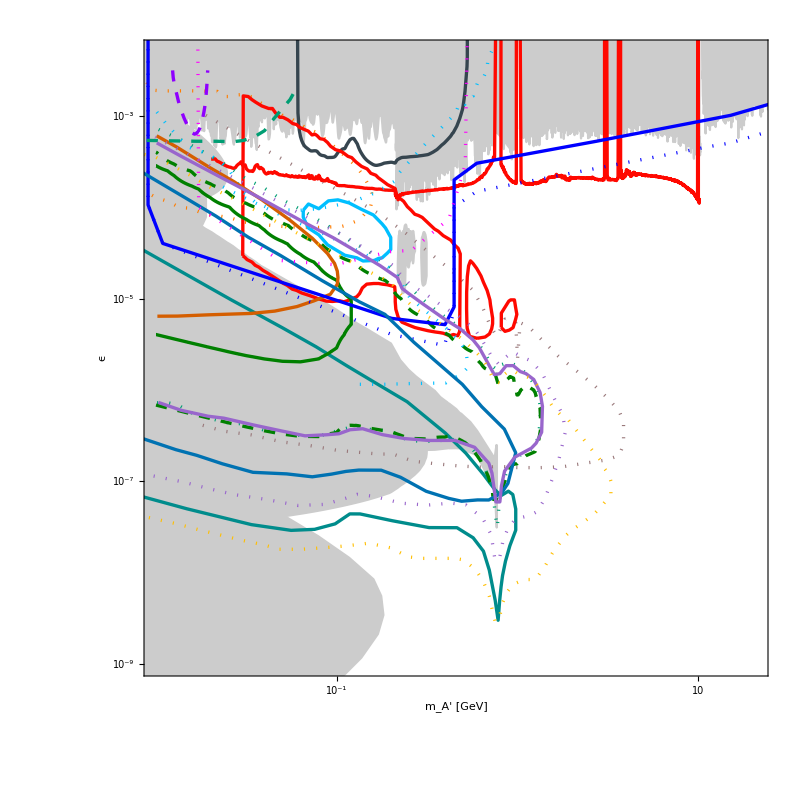

```mathematica
(* Final *)
Shades={ShadeEWPTCurtin2014,ShadeA1Merkel2014avp,ShadeAMMeBodas2021fsyrb,ShadeAMMmuBodas2021fsy,ShadeAPEXAbrahamyan2011gv,ShadeBaBarLees2014xha,ShadeBESIIIAblikim2017aab,ShadeCHARMTsai2019mtm,ShadeCMSCMS2019kiy,ShadeE137Andreas2012mt,ShadeE141Riordan1987aw,ShadeE774Bross1989mp,ShadeOrsayDavier1989wz,ShadeKLOEAnastasi2018azpcombined,ShadeLHCbAaij2017rftprompt,ShadeLHCbAaij2019bvgprompt,ShadeLHCb2019displaced1,ShadeLHCb2019displaced2,ShadeNA48Batley2015lha,ShadeNA64Banerjee2019hmi,ShadeNuCALTsai2019mtm,ShadeSN1987AChang2019};

Lines={LineEWPTCurtin2014,LineA1Merkel2014avp,LineAMMeBodas2021fsyrb,LineAMMmuBodas2021fsy,LineAPEXAbrahamyan2011gv,LineBaBarLees2014xha,LineBESIIIAblikim2017aab,LineCHARMTsai2019mtm,LineCMSCMS2019kiy,LineE137Andreas2012mt,LineE141Riordan1987aw,LineE774Bross1989mp,LineOrsayDavier1989wz,LineKLOEAnastasi2018azpcombined,LineLHCbAaij2017rftprompt,LineLHCbAaij2019bvgprompt,LineLHCb2019displaced1,LineLHCb2019displaced2,LineNA48Batley2015lha,LineNA64Banerjee2019hmi,LineNuCALTsai2019mtm,LineSN1987AChang2019};

Projs={ProjILCeMBDKanemura2015,ProjDUNE10evt,ProjMUonEGalon2022,ProjMuonBD1e20MuOTCesarotti,ProjAPEXEssig2010xa,ProjBelleIIKou2018nap,ProjBelleIIdisplacedFerber2022low,ProjBelleIIdisplacedFerber2022med,ProjBelleIIdisplacedFerber2022high,ProjDarkLight17552022,ProjFACET2022,ProjFASERAriga2018ukuhllhc,ProjFASERAriga2018ukurun3,ProjHPSBaltzell2022displacedfull,ProjHPS2Baltzell2022,ProjhiHPSBaltzell2022,ProjLDMXvisible16GeV1e18EOT2018,ProjLHCb2022Run3,ProjLHCb2022Run6,ProjMu3ePSI2022,ProjNA62dump2020,ProjREDTOPcombined2022,ProjSeaQuestP1Gori,ProjSeaQuestP2Gori,ProjSHiPAhdida2020VMDCombined(*,ProjVEPP3Wojtsekhowski2012zq*)};

(*Plots*)
ShadeV=Show[Shades];
LineV=Show[Lines];
ProjV=Show[Projs,PlotRange->{{-3,2},{-12,-1.99}}];
FigV1=Show[FigFrame,ShadeV,ProjV,PlotRange->{{Log10[0.01],1},{-9,-1.9999}},AspectRatio->3/4];
FigV1=Show[FigFrame,ShadeV,LineV,PlotRange->{{Log10[0.01],Log10[11]},{-9,Log10[0.1001]}},AspectRatio->1];
FigV1=Show[FigFrame,ShadeV,ProjV,PlotRange->{{Log10[0.01],Log10[21]},{Log10[ 1 10^-9],Log10[0.005]}},AspectRatio->1]
```

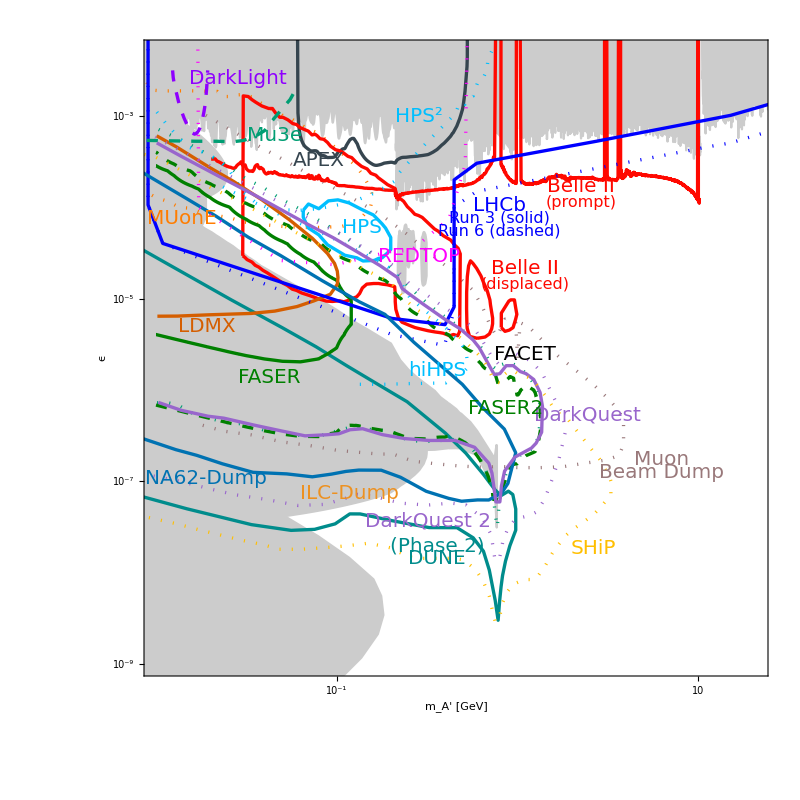

```mathematica
(* Label plot *)
FSlabel=20;
FSsublabel=16;Figlabel=Graphics[{
Text[Rotate[Style["HPS",HPSColor,FontSize->FSlabel],0.0],Scaled[{0.35,0.705}]],
Text[Rotate[Style["hiHPS",HPSColor,FontSize->FSlabel],0.0],Scaled[{0.47,0.48}]],
Text[Style["APEX",APEXColor,FontSize->FSlabel],Scaled[{0.28,0.81}]],
Text[Style["Belle II",Belle2Color,FontSize->FSlabel],Scaled[{0.7,0.77}]],
Text[Style["(prompt)",Belle2Color,FontSize->FSsublabel],Scaled[{0.7,0.745}]],
Text[Style["Belle II",Belle2Color,FontSize->FSlabel],Scaled[{0.61,0.64}]],
Text[Style["(displaced)",Belle2Color,FontSize->FSsublabel],Scaled[{0.61,0.615}]],Text[Style["LHCb",LHCbColor,FontSize->FSlabel],Scaled[{0.57,0.74}]],
Text[Style["Run 3 (solid)",LHCbColor,FontSize->FSsublabel],Scaled[{0.57,0.72}]],
Text[Style["Run 6 (dashed)",LHCbColor,FontSize->FSsublabel],Scaled[{0.57,0.7}]],
Text[Style["Muon",MuonBDColor,FontSize->FSlabel],Scaled[{0.83,0.34}]],Text[Style["Beam Dump",MuonBDColor,FontSize->FSlabel],Scaled[{0.83,0.32}]],Text[Style["SHiP",SHiPColor,FontSize->FSlabel],Scaled[{0.72,0.2}]],Text[Style["DarkQuest",DarkQuestColor,FontSize->FSlabel],Scaled[{0.71,0.41}]],Text[Style["DarkQuest 2",DarkQuestColor,FontSize->FSlabel],Scaled[{0.455,0.243}]],Text[Style["NA62-Dump",NA62DumpColor,FontSize->FSlabel],Scaled[{0.1,0.31}]],Text[Style["FASER",FASERColor,FontSize->FSlabel],Scaled[{0.2,0.47}]],Text[Style["FASER2",FASERColor,FontSize->FSlabel],Scaled[{0.58,0.42}]],
Text[Style["FACET",FACETRGB,FontSize->FSlabel],Scaled[{0.61,0.505}]],Text[Style["LDMX",LDMXColor,FontSize->FSlabel],Scaled[{0.1,0.55}]],Text[Style["HPS^2",HPSColor,FontSize->FSlabel],Scaled[{0.44,0.88}]],Text[Style["Mu3e",MuonColor,FontSize->FSlabel],Scaled[{0.21,0.85}]],Text[Style["DarkLight",DarkLightColor,FontSize->FSlabel],Scaled[{0.15,0.94}]],Text[Style["MUonE",MUonEColor,FontSize->FSlabel],Scaled[{0.06,0.72}]],Text[Style["REDTOP",REDTOPColor,FontSize->FSlabel],Scaled[{0.44,0.66}]],Text[Style["(Phase 2)",DUNEColor,FontSize->FSlabel],Scaled[{0.47,0.205}]],Text[Style["DUNE",DUNEColor,FontSize->FSlabel],Scaled[{0.47,0.185}]],Text[Style["ILC-Dump",ILCColor,FontSize->FSlabel],Scaled[{0.33,0.287}]]
}];
FigArrow=Graphics[{Thick,{Arrowheads[Medium],Arrow[{{0.4,-8.15},{0.375,-8}}]}}];
FigLine=Graphics[{Thickness[0.01],{Line[{{-1.2,-8},{-1.3,-8}}]}}];
FigV2=Show[FigV1,Figlabel]
```

```mathematica
Export[NBlocation<>"/Vector-Portal-All.pdf",FigV2]
```

/Users/batell/Desktop/vector-portal/Vector-Portal-All.pdf

## Final plot --current limits, Belle 2, DUNE, LHCb

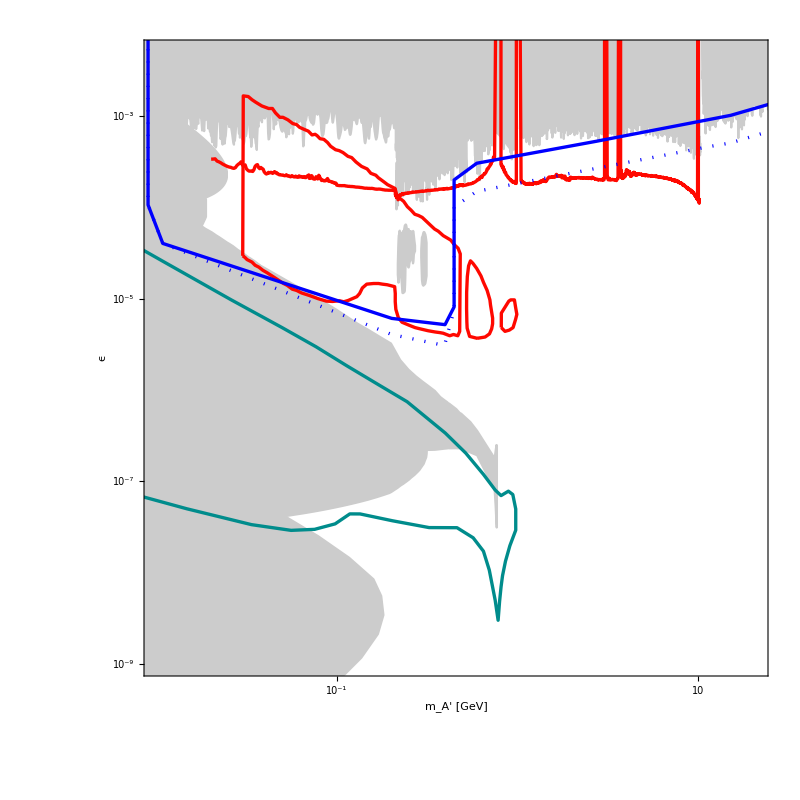

```mathematica
(* Final *)

Shades={ShadeEWPTCurtin2014,ShadeA1Merkel2014avp,ShadeAMMeBodas2021fsyrb,ShadeAMMmuBodas2021fsy,ShadeAPEXAbrahamyan2011gv,ShadeBaBarLees2014xha,ShadeBESIIIAblikim2017aab,ShadeCHARMTsai2019mtm,ShadeCMSCMS2019kiy,ShadeE137Andreas2012mt,ShadeE141Riordan1987aw,ShadeE774Bross1989mp,ShadeOrsayDavier1989wz,ShadeKLOEAnastasi2018azpcombined,ShadeLHCbAaij2017rftprompt,ShadeLHCbAaij2019bvgprompt,ShadeLHCb2019displaced1,ShadeLHCb2019displaced2,ShadeNA48Batley2015lha,ShadeNA64Banerjee2019hmi,ShadeNuCALTsai2019mtm,ShadeSN1987AChang2019};

Lines={LineEWPTCurtin2014,LineA1Merkel2014avp,LineAMMeBodas2021fsyrb,LineAMMmuBodas2021fsy,LineAPEXAbrahamyan2011gv,LineBaBarLees2014xha,LineBESIIIAblikim2017aab,LineCHARMTsai2019mtm,LineCMSCMS2019kiy,LineE137Andreas2012mt,LineE141Riordan1987aw,LineE774Bross1989mp,LineOrsayDavier1989wz,LineKLOEAnastasi2018azpcombined,LineLHCbAaij2017rftprompt,LineLHCbAaij2019bvgprompt,LineLHCb2019displaced1,LineLHCb2019displaced2,LineNA48Batley2015lha,LineNA64Banerjee2019hmi,LineNuCALTsai2019mtm,LineSN1987AChang2019};

Projs={ProjDUNE10evt,ProjBelleIIKou2018nap,ProjBelleIIdisplacedFerber2022low,ProjBelleIIdisplacedFerber2022med,ProjBelleIIdisplacedFerber2022high,ProjLHCb2022Run3,ProjLHCb2022Run6};

(*Plots*)
ShadeV=Show[Shades];
LineV=Show[Lines];
ProjV=Show[Projs,PlotRange->{{-3,2},{-12,-1.99}}];
FigV1=Show[FigFrame,ShadeV,ProjV,PlotRange->{{Log10[0.01],1},{-9,-1.9999}},AspectRatio->3/4];
FigV1=Show[FigFrame,ShadeV,LineV,PlotRange->{{Log10[0.01],Log10[11]},{-9,Log10[0.1001]}},AspectRatio->1];
FigV1=Show[FigFrame,ShadeV,ProjV,PlotRange->{{Log10[0.01],Log10[21]},{Log10[ 1 10^-9],Log10[0.005]}},AspectRatio->1]
```

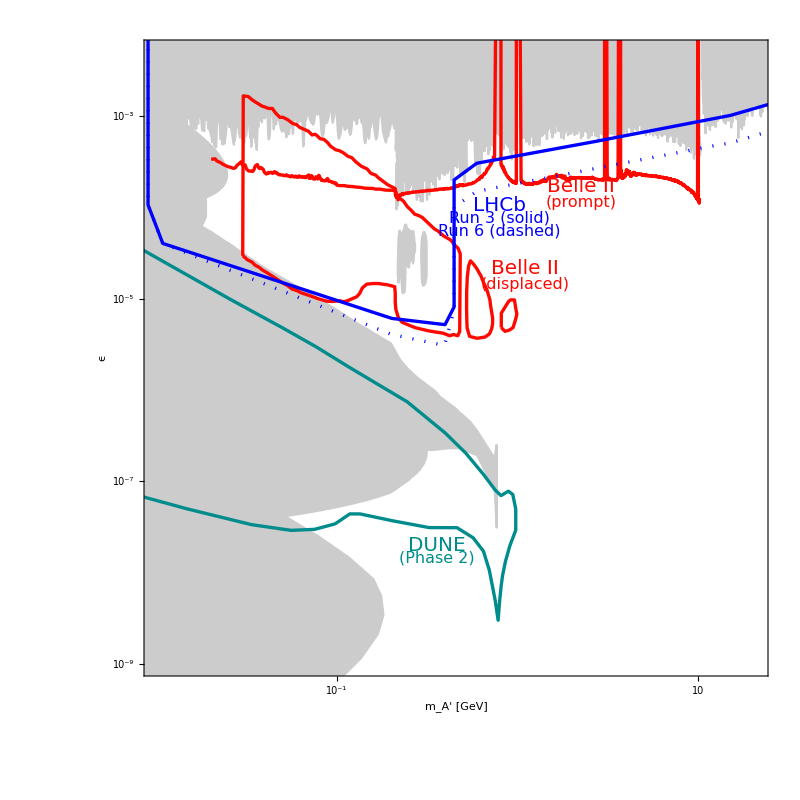

```mathematica
FSlabel=20;
FSsublabel=16;Figlabel=Graphics[{
(*Text[Rotate[Style["HPS",HPSColor,FontSize->FSlabel],0.0],Scaled[{0.35,0.705}]],
Text[Rotate[Style["hiHPS",HPSColor,FontSize->FSlabel],0.0],Scaled[{0.47,0.48}]],
Text[Style["APEX",APEXColor,FontSize->FSlabel],Scaled[{0.28,0.81}]],*)
Text[Style["Belle II",Belle2Color,FontSize->FSlabel],Scaled[{0.7,0.77}]],
Text[Style["(prompt)",Belle2Color,FontSize->FSsublabel],Scaled[{0.7,0.745}]],
Text[Style["Belle II",Belle2Color,FontSize->FSlabel],Scaled[{0.61,0.64}]],
Text[Style["(displaced)",Belle2Color,FontSize->FSsublabel],Scaled[{0.61,0.615}]],Text[Style["LHCb",LHCbColor,FontSize->FSlabel],Scaled[{0.57,0.74}]],
Text[Style["Run 3 (solid)",LHCbColor,FontSize->FSsublabel],Scaled[{0.57,0.72}]],
Text[Style["Run 6 (dashed)",LHCbColor,FontSize->FSsublabel],Scaled[{0.57,0.7}]],
(*Text[Style["Muon",MuonBDColor,FontSize->FSlabel],Scaled[{0.83,0.34}]],Text[Style["Beam Dump",MuonBDColor,FontSize->FSlabel],Scaled[{0.83,0.32}]],Text[Style["SHiP",SHiPColor,FontSize->FSlabel],Scaled[{0.72,0.2}]],Text[Style["DarkQuest",DarkQuestColor,FontSize->FSlabel],Scaled[{0.71,0.41}]],Text[Style["DarkQuest 2",DarkQuestColor,FontSize->FSlabel],Scaled[{0.455,0.243}]],Text[Style["NA62-Dump",NA62DumpColor,FontSize->FSlabel],Scaled[{0.1,0.31}]],Text[Style["FASER",FASERColor,FontSize->FSlabel],Scaled[{0.2,0.47}]],Text[Style["FASER2",FASERColor,FontSize->FSlabel],Scaled[{0.58,0.42}]],
Text[Style["FACET",FACETRGB,FontSize->FSlabel],Scaled[{0.61,0.505}]],Text[Style["LDMX",LDMXColor,FontSize->FSlabel],Scaled[{0.1,0.55}]],Text[Style["HPS^2",HPSColor,FontSize->FSlabel],Scaled[{0.44,0.88}]],Text[Style["Mu3e",MuonColor,FontSize->FSlabel],Scaled[{0.21,0.85}]],Text[Style["DarkLight",DarkLightColor,FontSize->FSlabel],Scaled[{0.15,0.94}]],Text[Style["MUonE",MUonEColor,FontSize->FSlabel],Scaled[{0.06,0.72}]],Text[Style["REDTOP",REDTOPColor,FontSize->FSlabel],Scaled[{0.44,0.66}]],*)Text[Style["DUNE",DUNEColor,FontSize->FSlabel],Scaled[{0.47,0.205}]],Text[Style["(Phase 2)",DUNEColor,FontSize->FSsublabel],Scaled[{0.47,0.185}]](*,Text[Style["ILC-Dump",ILCColor,FontSize->FSlabel],Scaled[{0.33,0.287}]]*)
}];
FigArrow=Graphics[{Thick,{Arrowheads[Medium],Arrow[{{0.4,-8.15},{0.375,-8}}]}}];
FigLine=Graphics[{Thickness[0.01],{Line[{{-1.2,-8},{-1.3,-8}}]}}];
FigV2=Show[FigV1,Figlabel]
```

```mathematica
Export[NBlocation<>"/Vector-Portal.pdf",FigV2]
```

/Users/batell/Desktop/vector-portal/Vector-Portal.pdf